This package has been rewritten to be self-contained, avoiding obsolete packages in the old system

28.4.19   There were some bugs here:
	- AddMutation got confused by nodes that are labelled as lists. I therefore removed the form which adds lists of mutations all at once

19.10.20  Updated slightly to allow mutations to be added to a population that changes in size through time (scaling current size to 1).

30.12.21 Added the option BranchStyle->f to modify  the style of each branch in PlotGenealogy

## Usage statements

### Describing genealogies

#### Node[i,{info},{Node[j,…],Node[k,…]}] denotes a node in a branching tree. This node is labelled by the integer i; information on it is given by {info}. The node has descendant nodes labelled j, k. A terminal node (a leaf) is denoted by Node[i,{info},{}].

```mathematica
Node::usage="Node[i,{info},{Node[j,…],Node[k,…]}] denotes a node in a branching tree.  This node is labelled by the integer i; information on it is given by {info}.  The node has descendant nodes labelled j, k.  A terminal node (a leaf) is denoted by Node[i,{info},{}].";
```

#### NodeFunction is an option for CollapseGenealogy and MakeGenealogy which can be set to extract information about each node.

```mathematica
NodeFunction::usage="NodeFunction is an option for CollapseGenealogy and MakeGenealogy which can be set to extract information about each node.";
```

#### ExtractGenealogy[g,i] gives the genealogy that descends from node i.

```mathematica
ExtractGenealogy::usage="ExtractGenealogy[g,i] gives the genealogy that descends from node i.  For an ancestral graph, ExtractGenealogy[{AncestralLineage[…]…},x] generates the genealogy corresponding to map position x. InformationFunction->f generates an information list f[i,x]. ExtractGenealogy[{AncestralLineage[…]…}] generates the set of genealogies, applying to segments demarcated by Junctions[g].  All parts of the genome must have a single common ancestor.";
```

#### DeleteGenealogy[g,i] deletes the genealogy that descends from node i.

```mathematica
DeleteGenealogy::usage="DeleteGenealogy[g,i] deletes the genealogy that descends from node i.";
```

#### AddGenealogy[g_1,g_2,i,j,info] adds genealogy g_2 to genealogy g_1, immediately above existing node i of g_1. The new node is labelled j, and carries information info.

```mathematica
AddGenealogy::usage="AddGenealogy[g_1,g_2,i,j,info] adds genealogy g_2 to genealogy g_1, immediately above existing node i of g_1.  The new node is labelled j.  The new node is labelled j, and carries information info.  If i=j, then g_2 is added to existing node i, and its information is unaltered.  Node i must be found once and only once within g_1.";
```

#### AddNode[g,i,k,info] adds a new node k immediately above existing node i of g. The new node carries information info. AddNode[g,i,j,k,info] adds a new node k between nodes i and j of an unrooted genealogy

```mathematica
AddNode::usage="AddNode[g,i,k,info] adds a new node k immediately above existing node i of g.  The new node carries information info.  AddNode[g,i,j,k,info] adds a new node k between nodes i and j of an unrooted genealogy.";
```

#### CondenseGenealogy[g] removes all nodes that have only one descendant.

```mathematica
CondenseGenealogy::usage="CondenseGenealogy[g] removes all nodes that have only one descendant. However, the root node is not affected. ";
```

#### Nodes[g] lists all the nodes of the genealogy g, including the leaves.

```mathematica
Nodes::usage="Nodes[g] lists all the nodes of the genealogy g, including the leaves. ";
```

#### InternalNodes[g] lists the internal nodes of the genealogy g.

```mathematica
InternalNodes::usage="InternalNodes[g] lists the internal nodes of the genealogy g. ";
```

#### Leaves[g] lists the terminal nodes of the genealogy g.

```mathematica
Leaves::usage="Leaves[g] lists the terminal nodes of the genealogy g. For an ancestral graph, Leaves[{AncestralLineage[…]…}] gives those lineages which start at times when no other lineages end";
```

#### CollapseGenealogy[genealogy] reduces the genealogy to a nested list. CollapseGenealogy[genealogy, Node→False] only lists the leaves.

```mathematica
CollapseGenealogy::usage="CollapseGenealogy[genealogy] reduces the genealogy to a nested list.  Node→False only lists the leaves. NodeFunction→f extracts a nested list of the information associated with each node, by applying f[i,{info}] to the full set of information contained in the genealogy. Nested→False does not preserve the nested structure.";
```

#### SizeOfGenealogyPlot[g] gives the minimum and maximum coordinates, held as the last element of the information lists in g.

```mathematica
SizeOfGenealogyPlot::usage="SizeOfGenealogyPlot[g] gives the minimum and maximum coordinates, held as the last element of the information lists in g, in the form {{x_min,y_min},{x_max,y_max}}.";
```

#### MakeGenealogyPlot[g] appends coordinates to the information lists; these are used by PlotGenealogy[].

```mathematica
MakeGenealogyPlot::usage="MakeGenealogyPlot[g] appends coordinates to the information lists; these are used by PlotGenealogy[].  The vertical coordinate is incremented in units of 1, and the vertical span equals the number of lineages, minus 1. ";
```

#### PlotGenealogy[g] plots a genealogy; the coordinates are held as the last element of the information lists. These may be generated by MakeGenealogyPlot[g]. PlotGenealogy[g,NodeFunction→f] uses f[i,info] to derive the vertical coordinate; this might represent coalescence time, for example.

```mathematica
PlotGenealogy::usage="PlotGenealogy[g] plots a genealogy.  PlotGenealogy[g,NodeFunction→f] uses f[i,info] to derive the coordinates; this might represent coalescence time, for example.  By default, nodes & leaves are labelled.  NodeLabels→None suppresses the labelling; NodeLabels→f uses f[i,info] to derive labels.  BranchStyle->f uses f[i,info] to specify the style of the branch that descends to this node; default is {Black}. MakeGenealogyPlot→False requires that  the coordinates are held as the last element of the information list.  By default, these are generated by MakeGenealogyPlot[g].";
```

#### BranchStyle is an option for PlotGenealogy that specifies the style of a branch.

```mathematica
BranchStyle::usage="BranchStyle is an option for PlotGenealogy that specifies the style of a branch.";
```

#### BranchGraphic

```mathematica
BranchGraphic::usage="BranchGraphic->f is an option for PlotGenealogy that specifies a function f[ancNode,descNode] that gives the whole branch. The default is False, in which case BranchStyle defines the style of the line.";
```

#### LeafOffset is an option for PlotGenealogy which determines the position of leaf labels.

```mathematica
LeafOffset::usage="LeafOffset is an option for PlotGenealogy which determines the position of leaf labels.";
```

#### NodeOffset is an option for PlotGenealogy which determines the position of node labels.

```mathematica
NodeOffset::usage="NodeOffset is an option for PlotGenealogy which determines the position of node labels.";
```

#### LeafLabels→f is an option for PlotGenealogy which uses f[i,info] to construct labels for the leaves; LeafLabels→None suppresses labels.

```mathematica
LeafLabels::usage="LeafLabels→f is an option for PlotGenealogy which uses f[i,info] to construct labels for the leaves; LeafLabels→None suppresses labels.";
```

#### MostRecentCommonAncestor[pop,i,j] gives the most recent common ancestor of nodes i, j

```mathematica
MostRecentCommonAncestor::usage="MostRecentCommonAncestor[g,i,j] gives the most recent common ancestor of nodes i, j.  ";
```

#### Nested is an option for CollapseGenealogy which determines whether the nested structure is preserved.

```mathematica
Nested::usage="Nested is an option for CollapseGenealogy which determines whether the nested structure is preserved. ";
```

#### ExtractInformation[g,i] gives the information associated with node i.

```mathematica
ExtractInformation::usage="ExtractInformation[g,i] gives the information associated with node i. ExtractInformation[g] gives a list of the information for all the nodes.  For an ancestral graph, ExtractInformation[{AncestralLineage[…]…},l] extracts the information associated with the lineage labelled by l.  Checks that there is only one such lineage. ExtractInformation[{AncestralLineage[…]…},{l_1,…}] extracts a list of such information. ";
```

#### TransformInformation[g,f] replaces the information list info by f[node,info].

```mathematica
TransformInformation::usage="TransformInformation[g,f] replaces the information list info by f[node,info].";
```

#### ListToGenealogy[list] constructs a genealogy from a nested list of the form {label,{node_1,node_2,…}}. Information on each node can be included using NodeFunction→f, where f[label] gives a list of information for the node with that label. ListToGenealogy[{{a,b},{c,d}},Node→False] gives a genealogy relating objects {a,b,…}. Internal nodes are unlabelled.

```mathematica
ListToGenealogy::usage="ListToGenealogy[list] constructs a genealogy from a nested list of the form {label,{node_1,node_2,…}}.  Information on each node can be included using NodeFunction→f, where f[label] gives a list of information for the node with that label.  ListToGenealogy[{{a,b},{c,d}},Node→False] gives a genealogy relating objects {a,b,…}.  Internal nodes are unlabelled.";
```

#### OrderedNodes[g,f] gives a list of the nodes in the genealogy, in the order defined by f[ i,{info}]

```mathematica
OrderedNodes::usage="OrderedNodes[g,f] gives a list of the nodes in the genealogy, in the order defined by f[ i,{info}].  OrderedNodes[g,f,Node→True] only lists internal nodes.";
```

#### Ancestors[g,node] lists the ancestors of the node.

```mathematica
Ancestors::usage="Ancestors[g,node] lists the ancestors of the node.  For an ancestral graph, Ancestors[{AncestralLineage[…],…},l] lists the immediate ancestors of lineage l.  MapPosition→x restricts the list to ancestors at map position x.  AncestorList→All gives a list of all ancestors, in  the form {l_1,{{d_1,{…}},{d_2,{…}}}}.  AncestorList→Roots gives only the root ancestors.  ";
```

#### Descendants[g,node] lists the immediate descendants of the node. Descendants[g,node,DescendantList→All] lists all the descendants of the node. Descendants[g,node,DescendantList→Leaves] lists only the descendant leaves of the node.

```mathematica
Descendants::usage="Descendants[g,node] lists the immediate descendants of the node.  Descendants[g,node,DescendantList→All] lists all the descendants of the node. Descendants[g,node,DescendantList→Leaves] lists only the descendant leaves of the node.  For an ancestral graph, Descendants[{AncestralLineage[…],…},l] lists the immediate descendants from lineage l.  MapPosition→x restricts the list to descendants at map position x.  DescendantList→All gives a list of all descendants, in  the form {l_1,{{d_1,{…}},{d_2,{…}}}}. DescendantList→Leaves gives only the descendant leaves.";
```

#### DescendantList is an option for Descendants[]; may be set to Next, All or Leaves.

```mathematica
DescendantList::usage="DescendantList is an option for Descendants[]; may be set to Next, All or Leaves.";
```

#### UnrootedGenealogy[g] gives an unrooted genealogy.

```mathematica
UnrootedGenealogy::usage="UnrootedGenealogy[g] gives an unrooted genealogy.";
```

#### RootedGenealogy[g,i] | roots an unrooted genealogy at node i

```mathematica
RootedGenealogy::usage="TextForm`RootedGenealogy[g,i] roots an unrooted genealogy at node i";
```

#### SiblingList[g] lists all pairs of leaves which are directly related.

```mathematica
SiblingList::usage="SiblingList[g] lists all pairs of leaves which are directly related.";
```

### Family structures

#### GenealogyToFamily[g,f] gives a list of the family structures following successive coalescences. The function f[i,{info}] gives the ordering of the coalescence for node i.

```mathematica
GenealogyToFamily::usage="GenealogyToFamily[g,f] gives a list of the family structures following successive coalescences. The function f[i,{info}] gives the ordering of the coalescence for node i.";
```

#### FamilyToGenealogy[{a,b,c,…},S] gives a randomly constructed genealogy which satistfies the sequence of family structures S, and which relates {a,b,c,…}. The terminal nodes are labelled by {a,b,c,…}, and the internal nodes are labelled by integers giving the order of the coalescence events. NodeLabels→{label_1,…} allows an arbitrary list of labels for the internal nodes. NodeInformation→{info_1,…}, LeafInformation→{info_a,…} allow arbitrary lists of information to be associated with the nodes and leaves. With n items, there are n nodes, and so all the optional lists must have length n.

```mathematica
FamilyToGenealogy::usage="FamilyToGenealogy[{a,b,c,…},S] gives a randomly constructed genealogy which satistfies the sequence of family structures S, and which relates {a,b,c,…}.  The terminal nodes are labelled by {a,b,c,…}, and the internal nodes are labelled by integers giving the order of the coalescence events. NodeLabels→{label_1,…} allows an arbitrary list of labels for the internal nodes.  NodeInformation→{info_1,…}, LeafInformation→{info_a,…} allow arbitrary lists of information to be associated with the nodes and leaves.  With n items, there are n nodes, and so all the optional lists must have length n.";
```

#### LeafInformation→{info_a,…} is an option for FamilyToGenealogy[] which specifies information associated with each leaf.

```mathematica
LeafInformation::usage="LeafInformation→{info_a,…} is an option for FamilyToGenealogy[] which specifies information associated with each leaf.";
```

#### NodeInformation→{info_1,…} is an option for FamilyToGenealogy[] which specifies information associated with each internal node. The number of such nodes is the same as the number of leaves; nodes are ordered by their timing.

```mathematica
NodeInformation::usage="NodeInformation→{info_1,…} is an option for FamilyToGenealogy[] which specifies information associated with each internal node.  The number of such nodes is the same as the number of leaves; nodes are ordered by their timing.";
```

#### NodeLabels→{label_1,…} is an option for FamilyToGenealogy[] which specifies labels for each internal node. The number of such nodes is the same as the number of leaves; nodes are ordered by their timing.

```mathematica
NodeLabels::usage="NodeLabels→{label_1,…} is an option for FamilyToGenealogy[] which specifies labels for each internal node.  The number of such nodes is the same as the number of leaves; nodes are ordered by their timing.  NodeLabels→f is an option for PlotGenealogy which uses f[i,info] to construct labels for the nodes; NodeLabels→None suppresses labels.";
```

#### GenealogyB[j,i,k] is the coefficient of Exp[-λ_it/2N] in the expression for P_j, the probability of j coalescences having occurred.

```mathematica
GenealogyB::usage="GenealogyB[j,i,k] is the coefficient of Exp[-λ_it/2N] in the expression for P_j, the probability of j coalescences having occurred.";
```

#### CoalescenceDistribution[j,k,t] is the probability of j coalescences having occurred among k lineages over t generations (scaled to 2N)

```mathematica
CoalescenceDistribution::usage="CoalescenceDistribution[j,k,t] is the probability of j coalescences having occurred among k lineages over t generations (scaled to 2N) ";
```

#### SimplifyFamilies replaces duplications such as {{1,3},{2,2},{2,1}} by {{1,3},{2,3}}

```mathematica
SimplifyFamilies::usage="SimplifyFamilies replaces duplications such as {{3,1},{2,2},{1,2}} by {{3,1},{3,2}}";
```

#### FamilyProbability[S] gives the probability that this family structure would be produced, given a certain number of coalescence events

```mathematica
FamilyProbability::usage="FamilyProbability[S] gives the probability that the family structure S would be produced, given a certain number of coalescence events.";
```

#### NumberOfLineages[S] gives the total number of genes involved

```mathematica
NumberOfLineages::usage="NumberOfLineages[g]  gives the total number of lineages (i.e., terminal nodes) involved in the genealogy g. NumberOfLineages[g,i] gives the number that descend from node i.  NumberOfLineages[S] can also be applied to a list of family sizes, S";
```

#### PairwiseIdentity[S] gives the mean pairwise identity

```mathematica
PairwiseIdentity::usage="PairwiseIdentity[S] gives the mean pairwise identity, given the family structure S.";
```

#### AllSets[j,k] lists all the family structures that could yield j families and k genes

```mathematica
AllSets::usage="AllSets[j,k] lists all the family structures that could yield j families and k genes";
```

#### NewS[S] gives a recursion for the family structures

```mathematica
NewS::usage="NewS[S] gives a recursion for the family structures";
```

#### NumberOfFamilies[S] gives the number of families

```mathematica
NumberOfFamilies::usage="NumberOfFamilies[S] gives the number of families";
```

### Random genealogies

#### CoalescenceTimes

```mathematica
CoalescenceTimes::usage="CoalescenceTimes is an option for RandomGenealogy.  CoalescenceTimes→Random uses RandomCoalescenceTimes[k]; otherwise a list of times must be supplied";
```

#### RandomCoalescenceTimes[k] gives a list of random coalescence times

```mathematica
RandomCoalescenceTimes::usage="RandomCoalescenceTimes[k] gives a list of random coalescence times, scaled to 2N generations. RandomCoalescenceTimes[n,k,R] generates a sequence of n coalescences and recombinations, starting with k lineages at t=0. The output is a list of n items of the form {t,k,j}, where t is the time of the event;k is the number of lineages after the event; and j is the location of the recombination event in the interval {0,R}. j=None indicates a coalescence.  RandomCoalescenceTimes[k,R] generates a single item, with rate k(k-1)/2 of coalescence and k R of recombination.";
```

#### RandomCoalescenceTimesG[k,λ] gives a list of random coalescence times for a population growing at rate λ

```mathematica
RandomCoalescenceTimesG::usage="RandomCoalescenceTimesG[k,λ] gives a list of random coalescence times, scaled to 2N generations, for a population growing at rate λ to current (scaled) size 1. This simply uses a scale transformation t=log[1+λt]/λ, which reduces the coalescence times deeper in the tree. Note that if λ<0 (a shrinking population) then lineages that do not coalesce by rescaled time 1/|λ| will never coalesce: coalescence times are then given as ∞.  ";
```

#### NumberOfCoalescences[k,T] gives a randomly sampled number of coalescence events that occur in T (scaled to 2N) NumberOfCoalescences[{t1,t2..}] does the same, for a list of coalescence times.

```mathematica
NumberOfCoalescences::usage="NumberOfCoalescences[k,T] gives a randomly sampled number of coalescence events that occur in T (scaled to 2N). NumberOfCoalescences[{t1,t2..},T] does the same, for a list of coalescence times. ";
```

#### TotalLength[{t1,t2,..}] is the total length of the tree

```mathematica
TotalLength::usage="TotalLength[{t1,t2,..}] is the total length of the tree, given the coalescence times.";
```

#### RandomFamilies[k] generates a list of the family sizes going back through time to the common ancestor of k genes.

```mathematica
RandomFamilies::usage="RandomFamilies[k] generates a list of the family sizes going back through time to the common ancestor of k genes.";
```

#### RandomPreviousFamily[{1,1,2,3}] generates a random coalescence to give the previous family structure

```mathematica
RandomPreviousFamily::usage="RandomPreviousFamily[{1,1,2,3}] generates a random coalescence to give the previous family structure";
```

#### RandomGenealogy[{leaf_1,leaf_2,…}] gives a random realisation of the coalescent process. Terminal nodes are labelled {leaf_1,leaf_2,…}, and internal nodes are labelled by an integer, in the order in which they occur. Each node carries its time, scaled to 2N generations. MutationRate→θ simulates infinite-sites mutation at a rate θ=4Nμ; mutations are labelled by unique integers. NodeLabels→{label_1,…} can be used to label internal nodes.

```mathematica
RandomGenealogy::usage="RandomGenealogy[{leaf_1,leaf_2,…}] gives a random realisation of the coalescent process.  Terminal nodes are labelled {leaf_1,leaf_2,…}, and internal nodes are labelled by an integer, in the order in which they occur.  Each node carries its time, scaled to 2N generations.  MutationRate→θ simulates infinite-sites mutation at a rate θ=4Nμ; mutations are labelled by unique integers. NodeLabels→{label_1,…} can be used to label internal nodes.   RandomGenealogy[{leaf_1,leaf_2…},n,R] gives a random realisation of the coalescent process with recombination; there are n events. RandomGenealogy[{leaf_1,leaf_2…},{{t_1,k_1,x_1}…},R] gives a random realisation for a specific sequence of events, generated by RandomCoalescenceTimes[n,k,R]; this preserves null lineages, however.  DeleteNullLineages->True ignores null events; can only be used with the first form. PrintDetails→True prints details of the construction.  MaxTime->t stops after time t.  Fixation->True stops when the whole genome is fixed.";
```

#### MutationRate→θ is an option for RandomGenealogy[] which sets the scaled mutation rate θ=4Nμ. Default is MutationRate→None.

```mathematica
MutationRate::usage="MutationRate→θ is an option for RandomGenealogy[] which sets the scaled mutation rate θ=4Nμ.  Default is MutationRate→None.";
```

#### DeletedMutations[g,{T_0,T_1}] lists those mutations that should be deleted because they occurred in time interval {T_0,T_1}. This list may be to some extent randomly generated.

```mathematica
DeletedMutations::usage="DeletedMutations[g,{T_0,T_1}] lists those mutations that should be deleted because they occurred in time interval {T_0,T_1}.  This list may be to some extent randomly generated. ";
```

#### RandomBottleneckedGenealogy[leaves,{T0,T1},θ] gives a random genealogy, with no mutations occurring in time interval {T0,T1}.

```mathematica
RandomBottleneckedGenealogy::usage="RandomBottleneckedGenealogy[leaves,{T0,T1},θ] gives a random genealogy, with no mutations occurring in time interval {T0,T1}.";
```

### Generating functions

#### MomentGeneratingFunction[g,ω,θ] gives the generating function for the number of mutations along each branch of the genealogy, under the infinite sites model.

```mathematica
MomentGeneratingFunction::usage="MomentGeneratingFunction[g,ω,θ] gives the generating function for the number of mutations along each branch of the genealogy, under the infinite sites model. MomentGeneratingFunction[{{a},{b},…},ω,θ] gives the generating function for all tree topologies, in terms of variables ω[S] which correspond to those mutations in branches ancestral to the set of leaves S. Stores results. ";
```

### The probability of genealogies

#### IncidenceMatrix[g,nodelist] gives the matrix describing an ordering of coalescences defined by nodelist. The last member of nodelist is the root node. The elements of the matrix show whether a branch is present during the time for which there are 1≤i≤n lineages. Rows correspond to branches, in the order specified by nodelist.

```mathematica
IncidenceMatrix::usage=IncidenceMatrix::usage<>"  For genealogies, IncidenceMatrix[g,nodelist] gives the matrix describing an ordering of coalescences defined by nodelist.  The last member of nodelist is the root node.  The elements of the matrix show whether a branch is present during the time for which there are 1≤i≤n lineages. Rows correspond to branches, in the order specified by nodelist. ";
```

#### MonteCarloProbability[g,nodelist,J,θ,ns] makes a Monte Carlo estimate of the probability of the genealogy g and the mutational configuration J, assuming that the coalescences are in the order specified by nodelist. A list of ns values is returned. MonteCarloProbability[g,J,θ,ns] makes no assumptions as to the order of events.

```mathematica
MonteCarloProbability::usage="MonteCarloProbability[g,nodelist,J,θ,θ^*,ns] makes a Monte Carlo estimate of the probability of the genealogy g and the mutational configuration J, assuming that the coalescences are in the order specified by nodelist. A list of ns values is returned. MonteCarloProbability[g,J,θ,θ^*,ns] makes no assumptions as to the order of events. Uses the arbitrary parameter θ^* to make random partitions.  θ^* must be a number, but θ can be symbolic.";
```

#### PossibleCoalescenceOrder[g] lists the possible orders in which coalescence events might occur; each is given by an ordered list of nodes.

```mathematica
PossibleCoalescenceOrder::usage="PossibleCoalescenceOrder[g] lists the possible orders in which coalescence events might occur; each is given by an ordered list of nodes.  Leaves are listed first, and the root node last.";
```

#### RandomCoalescenceOrder[g] gives a random ordering of the possible coalescence events

```mathematica
RandomCoalescenceOrder::usage="RandomCoalescenceOrder[g] gives a random ordering of the possible coalescence events";
```

#### NumberOfPossibleCoalescences[g,nodelist] gives the number of possible coalescences that could occur at each step. Only internal nodes are included. The order of coalescences is defined by nodelist

```mathematica
NumberOfPossibleCoalescences::usage="NumberOfPossibleCoalescences[g,nodelist] gives the number of possible coalescences that could occur at each step. Only internal nodes are included. The order of coalescences is defined by nodelist";
```

#### NumberOfMutations[g,node] gives the number of mutations that occurred on the branch leading down to the specified node. The set of mutations is given in the second element of the information for each node.

```mathematica
NumberOfMutations::usage="NumberOfMutations[g,node] gives the number of mutations that occurred on the branch leading down to the specified node. The set of mutations is given in the second element of the information for each node. ";
```

#### Mutations[g] gives the set of mutations that occured on g. Mutations[g,i] gives the mutations that arose on the branch leading down to node i. By default, these are held in the second element of the information list. NodeFunction→f uses f[i,info] to extract the mutation list.

```mathematica
Mutations::usage="Mutations[g] gives the set of mutations that occured on g.  Mutations[g,i] gives the mutations that arose on the branch leading down to node i.  By default, these are held in the second element of the information list.  NodeFunction→f uses f[i,info] to extract the mutation list.";
```

#### MutationOrigin[g,k] gives the first node at which mutation k appears.

```mathematica
MutationOrigin::usage="MutationOrigin[g,k] gives the first node at which mutation k appears.   By default, the mutations are held in the second element of the information list, and the coalescence time as the first element.  NodeFunction→f uses f[i,info] to return {time,mutations}.";
```

#### MutationInterval[g,k] gives the time .interval in which mutation k arose.

```mathematica
MutationInterval::usage="MutationInterval[g,k] gives the time interval in which mutation k arose.  By default, the mutations are held in the second element of the information list, and the coalescence time as the first element.  NodeFunction→f uses f[i,info] to return {time,mutations}.";
```

#### ExactProbability[g,θ] gives the probability of this genealogy, given a scaled mutation rate θ=4Nμ. By default, the number of mutations is deduced from a list of unique mutations held in the second element of the information list. NodeFunction→f uses f[i,info] to find the number of mutations. Uses MomentGeneratingFunction[], and so is intractable for large numbers of mutations and for large genealogies. ExactProbability[S,θ] uses the generating function over all topologies to find the net probability of the configuration of mutations represented by the matrix S.

```mathematica
ExactProbability::usage="ExactProbability[g,θ] gives the probability of this genealogy, given a scaled mutation rate θ=4Nμ. By default, the number of mutations is deduced from a list of unique mutations held in the second element of the information list.  NodeFunction→f uses f[i,info] to find the number of mutations. Uses MomentGeneratingFunction[], and so is intractable for large numbers of mutations and for large genealogies.  ExactProbability[S,θ] uses the generating function over all topologies to find the net probability of the configuration of mutations represented by the matrix S.";
```

#### GenealogyToMatrix[g] gives a matrix whose rows specify which mutations are found in which leaf of the genealogy. By default, the list of mutations is taken from the second element of the information list. NodeFunction→f uses f[i,info] to specify the mutations in each node.

```mathematica
GenealogyToMatrix::usage="GenealogyToMatrix[g] gives a matrix whose rows specify which mutations are found in which leaf of the genealogy. The genealogy can be unrooted. By default, the list of mutations is taken from the second element of the information list.  NodeFunction→f uses f[i,info] to specify the mutations in each node.  MutationLabels->{m_1,…} specifies the names of the mutations; by default, the list is the set of mutations found in g.";
```

#### MatrixToGenealogy[S,{leaf_1, leaf_2,…},{μ_1,…}] constructs a genealogy from the matrix S. The leaves are labelled by {leaf_1, …} and the mutations by {μ_1,…}; internal nodes are labelled by unique integers

```mathematica
MatrixToGenealogy::usage="MatrixToGenealogy[S,{leaf_1, leaf_2,…},{μ_1,…}] constructs a genealogy from the matrix S.  The leaves are labelled by {leaf_1, …} and the mutations by {μ_1,…}; internal nodes are labelled by unique integers.  Unrooted->True yields an unrooted genealogy; no assumption is made as to which allele is ancestral and which derived.";
```

#### MatrixToList[S] converts a matrix representation to a list of the mutations held by each leaf. By default, mutations are numbered 1,2…. MutationLabels→{m_1,…} uses the specified labels.

```mathematica
MatrixToList::usage="MatrixToList[S] converts a matrix representation to a list of the mutations held by each leaf.  By default, mutations are numbered 1,2….  MutationLabels→{m_1,…} uses the specified labels.";
```

#### FindNode[g,{m_1,…},newNode] finds from where in the genealogy g a leaf carrying mutations {m_1,…} descends. If no node or branch matches, returns $Failed. If the leaf joins the branch above node i, returns {i,newNode,{m_1,…}}, where newNode is a new node label, distinct from any other in g. The last element lists the mutations carried at the new node. If the leaf joins at node i, returns {i,i,{m_1,…}}, where the last element lists the mutations carried at node i. The new leaf MUST contain all the mutations in the root node of g.

```mathematica
FindNode::usage="FindNode[g,{m_1,…},newNode] finds from where in the genealogy g a leaf carrying mutations {m_1,…} descends.  If no node or branch matches, returns $Failed. If the leaf joins the branch above node i, returns {i,newNode,{m_1,…}}, where newNode is a new node label, distinct from any other in g. The last element lists the mutations carried at the new node.  If the leaf joins at node i, returns {i,i,{m_1,…}}, where the last element lists the mutations carried at node i.    The new leaf MUST contain all the mutations in the root node of g, and g must carry at least one mutation on each branch, except for branches loeading down to leaves.";
```

#### MutationLabels→{m_1,…} is an option for MatrixToList[] which labels the mutations as {m_1,…}

```mathematica
MutationLabels::usage="MutationLabels is an option for MatrixToList[] which labels the mutations.";
```

#### ListToMatrix[{{1,2,3},{4},…}] converts a list of mutations present at each node into a matrix representation. MutationLabels→{m_1,…} gives the columns in the specified order.

```mathematica
ListToMatrix::usage="ListToMatrix[{{1,2,3},{4},…}] converts a list of mutations present at each node into a matrix representation.  MutationLabels→{m_1,…} gives the columns in the specified order.";
```

#### GriffithsTavare[S,θ] uses the Griffiths-Tavare algorithm to find the probability of a configuration of mutations defined by the matrix S.

```mathematica
GriffithsTavare::usage="GriffithsTavare[S,θ] uses the Griffiths-Tavare algorithm to find the probability of a configuration of mutations defined by the matrix S.";
```

#### MonteCarloGriffithsTavare[S,θ] uses the Monte-Carlo Griffiths-Tavare algorithm to find the probability of a configuration of mutations defined by the matrix S.

```mathematica
MonteCarloGriffithsTavare::usage="MonteCarloGriffithsTavare[S,θ] uses the Monte-Carlo Griffiths-Tavare algorithm to find the probability of a configuration of mutations defined by the matrix S.";
```

#### ValidMatrixQ

```mathematica
ValidMatrixQ::usage="ValidMatrixQ[S] determines whether a matrix of mutations, S, is compatible with a genealogy. The i'th row of S is a list of {1,0,…} representing the set of mutations present in the i'th leaf. Unrooted→True does not assume that a '1' represents a new mutation: 0, 1 just represent two alternative alleles. ValidMatrixQ[{0,1…},{1,0,…}] tests a particular pair of mutations.";
```

#### Unrooted

```mathematica
Unrooted::usage="Unrooted is an option for ValidMatrixQ which specifies that the genealogy is unrooted - i.e., no assumption is made about which allele is ancestral";
```

#### SwapStates

```mathematica
SwapStates::usage="SwapStates[s,S] swaps the states of mutations listed in the matrix S, according to the specification s.  The matrix S has dimensions # leaves×# mutations, and s is a vector of length equal to the # of mutations.  Both consist of 0 or 1.";
```

#### MissingCombination

```mathematica
MissingCombination::usage="MissingCombination[S] tabulates the missing combinations for each pair of mutations listed in S.  Each element contains {} if there are less than 3 combinations for that pair.  If there are 4 combinations, the matrix is invalid, and an error message is returned.  If there are three combinations, the missing combination is returned; swaps represented by this combination are not allowed.  Stores results.";
```

#### PossibleRootings

```mathematica
PossibleRootings::usage="PossibleRootings[S] lists all valid ways of rooting the mutations listed in S. Returns a list, in which each row {0,1,…} indicates whether an allele `1` is to be taken as ancestral (1) or derived (0). PossibleRootings[{{Null,0,1,Null…},…},S] eliminates indeterminate mutations, indicated by Null, until the solution is found.";
```

#### AddMutation

```mathematica
AddMutation::usage="AddMutation[n,m,g] adds the mutations m to node n; m can be one mutation,or a list of mutations. ";
```

```mathematica
(*AddMutation[{Subscript[n, 1],Subscript[n, 2],…},{Subscript[m, 1],Subscript[m, 2],…},g] adds to a list of nodes. Mutations are held as the second element of the information list.  ";*)
```

#### CondenseMatrix

```mathematica
CondenseMatrix::usage="CondenseMatrix[S] reduces the matrix S to the minimum informative size. Columns depicting mutations with the same distribution across leaves, mutations fixed across the whole set, or present in only one leaf, are removed.  Unrooted->True also removes one of each pair of complementary mutations (e.g. {0,0,1,1} and {1,1,0,0}).";
```

### Recombination

#### AncestralLineage

```mathematica
AncestralLineage::usage="AncestralLineage[l, {t0, t1}, {{a, b}, {}, {c, d}, {c}}, {r1, r2, r3, R}, {info}] represents one lineage in an ancestral graph.  It gives the name of the lineage, l; the timespan, {t0,t1}; the leaves which descend from the various segments, {{a,b},{},{c,d},{c}}; and the rightmost positions of each segment, {r1,r2,r3,R}.  The genome spans {0,R}.";
```

#### AncestralGraphPattern

```mathematica
AncestralGraphPattern::usage="AncestralGraphPattern is matched by a list {AncestralLineage[…]...}, representing an ancestral graph. No detailed checks are made that this is a valid graph, however.";
```

#### AncestralLineagePattern

```mathematica
AncestralLineagePattern::usage="AncestralLineagePattern is matched by an AncestralLineage[…]";
```

#### ExtractLabel

```mathematica
ExtractLabel::usage="ExtractLabel is a rule which replaces AncestralLineage[l,…] by its label, l.";
```

#### CoalesceLineages

```mathematica
CoalesceLineages::usage="CoalesceLineages[AncestralLineage[l1,…],AncestralLineage[l2,…],l12,t] gives a lineage l12 which is ancestral to l1, l2, generated by a coalescence event at time t.  By default, corresponding elements of information lists are put into a set; InformationFunction→f generates a new information list f[i_1,i_2]";
```

#### InformationFunction

```mathematica
InformationFunction::usage="InformationFunction->f is an option for functions dealing with ancestral graphs, which specifies how the information associated with each lineage should be handled.";
```

#### RecombineLineage

```mathematica
RecombineLineage::usage="RecombineLineage[AncestralLineage[l,…],{lL,lR},x,t] generates two recombinant lineages, with breakpoint at map position x, and labelled lL, lR. By default, the information lists are duplicated; InformationFunction→{fL,fR} generates a pair of information lists {fL[i],fR[i]}.";
```

#### Junctions

```mathematica
Junctions::usage="Junctions[AncestralLineage[…]] lists the junctions present in the lineage.  Junctions[{AncestralLineage[…]…}] lists all the junctions present in the ancestral graph. ";
```

#### MapLength

```mathematica
MapLength::usage="MapLength[AncestralLineage[…]] or MapLength[{AncestralLineage[…]…}] gives the map length, R. ";
```

#### LineagesPresent

```mathematica
LineagesPresent::usage="LineagesPresent[{AncestralLineage[…],…},t] gives the set of lineages present at time t. LineagesPresent[{AncestralLineage[…],…}] lists all lineages";
```

#### RecombinantLineages

```mathematica
RecombinantLineages::usage="RecombinantLineages[{AncestralLineage[…]…}] gives lineages which start at the same time as a sister lineage";
```

#### CoalescentLineages

```mathematica
CoalescentLineages::usage="CoalescentLineages[{AncestralLineage[…]…}] gives lineages which start at the same time as two other lineages end";
```

#### RootLineages

```mathematica
RootLineages::usage="RootLineages[{AncestralLineage[…]…}] gives lineages which end when no other lineages begin.";
```

#### ExtractLineage

```mathematica
ExtractLineage::usage="ExtractLineage[{AncestralLineage[…]…},l] extracts the lineage labelled by l. Checks that there is only one such lineage. ExtractLineage[{AncestralLineage[…]…},{l_1,…}] extracts a list of lineages. ";
```

#### ExtractLineagesEndingAtT

```mathematica
ExtractLineagesEndingAtT::usage="ExtractLineagesEndingAtT[{AncestralLineage[…]…},t] extracts those lineages which end at time t.  These are either root lineages, with no ancestors, or are generated by a coalescence or recombination.  Checks that these are present in the appropriate numbers.";
```

#### ExtractLineagesStartingAtT

```mathematica
ExtractLineagesStartingAtT::usage="ExtractLineagesStartingAtT[{AncestralLineage[…]…},t] extracts those lineages which start at time t.  These are either leaves, with no descendants, or are generated by a coalescence or recombination.  Checks that these are present in the appropriate numbers.";
```

#### TimesOfEvents

```mathematica
TimesOfEvents::usage="TimesOfEvents[{AncestralLineage[…]…}] lists all the times at which lineages begin or end.";
```

#### AllEvents

```mathematica
AllEvents::usage="AllEvents[{AncestralLineage[…]…}] lists all events at which lineages begin or end, in the form {t,descendants,ancestors,map position}. (The last element is set if there has been a recombination event; otherwise it is None).";
```

CoalescenceEvents

```mathematica
CoalescenceEvents::usage="CoalescenceEvents[{AncestralLineage[…]…}] lists events at which lineages {l_1,…} coalesce into lineage l_p, in the form {t,{l_1,l_2},l_P}.";
```

NullLineages

```mathematica
NullLineages::usage="NullLineages[g] lists those lineages which contain no material ancestral to the sample.";
```

RecombinationEvents

```mathematica
RecombinationEvents::usage="RecombinationEvents[{AncestralLineage[…]…}] lists events at which a lineages l_1 splits into two lineage {l_L, l_R} in the form {t,{l_p},{l_L,l_R},r}.";
```

NullRecombinationEvents

```mathematica
NullRecombinationEvents::usage="NullRecombinationEvents[{AncestralLineage[…]…}] lists events at which a lineages l_1 splits into two lineages {l_L, l_R}, but where one of these is null.  These have the form {t,{l_p},{l_L,l_R},R}.";
```

LeafEvents

```mathematica
LeafEvents::usage="LeafEvents[{AncestralLineage[…]…}] lists events at which a lineages becomes extinct.";
```

RootEvents

```mathematica
RootEvents::usage="RootEvents[{AncestralLineage[…]…}] lists events at which an ancestral lineage begins.";
```

TimespanOfLineage

```mathematica
TimespanOfLineage::usage="TimespanOfLineage[{AncestralLineage[…]…},l] gives the start and end times,{t0,t1}, of lineage l.";
```

MapPosition

```mathematica
MapPosition::usage="MapPosition→x is an option for Descendants which specifies that only descendants at map position x are counted.";
```

AddDescendants

```mathematica
AddDescendants::usage="AddDescendants[g,{l}] returns {l,Descendants[g,l]}.";
```

#### AncestorList

```mathematica
AncestorList::usage="AncestorList is an option for Ancestors; it may be set to Previous, All or Roots";
```

#### AddAncestors

```mathematica
AddAncestors::usage="AddAncestors[g,{l}] returns {l,Ancestors[g,l]}.";
```

#### DeleteNullLineages

```mathematica
DeleteNullLineages::usage="DeleteNullLineages[g] deletes ancestral lineages that have no descedants.  DeleteNullLineages is also an option for AddRecombinantLineages which specifies whether lineages carrying no material ancestral to thhe sample are to be included.";
```

#### AddRecombinantLineages

```mathematica
AddRecombinantLineages::usage="AddRecombinantLineages[g,l,{lL,lR},x,t] terminates lineage l, and adds two recombinant lineages {lL,lR} to the list g. DeleteNullLineages->True ignores null recombination events.";
```

#### AddCoalescentLineage

```mathematica
AddCoalescentLineage::usage="AddCoalescentLineage[g,{l1,l2},lC,t] terminates lineages {l1,l2} at t, and adds a coalescent lineage lC to the list g.";
```

#### PrintDetails

```mathematica
PrintDetails::usage="PrintDetails is an option for RandomGenealogy";
```

#### Segments

```mathematica
Segments::usage="Segments[AncestralLineage[…],l] gives the blocks ancestral to l present within the lineage.  Segments[{AncestralLineage[…]…},l] applies to several lineages";
```

#### PlotSegments

```mathematica
PlotSegments::usage="PlotSegments[AncestralLineage[…],leaf,y] gives a Graphics[] object depicting the segments ancestral to the leaf; drawn at height y.  SegmentStyle→{Blue,…} and BackgroundStyle→{Yellow,…} set the style of the lines.  PlotSegments[{AncestralLineage[…]…},leaf,{y0,y1}] plots a series of lineages spanning {y0,y1}; JunctionStyle specifies vertical lines depicting the junctions. ";
```

#### BackgroundStyle

```mathematica
BackgroundStyle::usage="BackgroundStyle is an option for PlotSegments which sets the style of non-ancestral parts of the chromosome; default {Yellow}";
```

#### SegmentStyle

```mathematica
SegmentStyle::usage="SegmentStyle is an option for PlotSegments which sets the style of ancestral parts of the chromosome; default {Blue}";
```

#### JunctionStyle

```mathematica
JunctionStyle::usage="JunctionStyle is an option for PlotSegments which sets the style of vertical lines depicting junctions; default {Black}";
```

#### TimeSpanOfJunctions

```mathematica
TimespanOfJunction::usage="TimespanOfJunction[{AncestralLineage[…]…},j] finds the first and last occurrence of j. ";
```

#### FixedQ

```mathematica
FixedQ::usage="FixedQ[AncestralLineage[…],lvs] tests whether this ancestral lineage only contains segments ancestral to the entire set lvs.  Can also apply to an ancestral graph";
```

#### MaxTime

```mathematica
MaxTime::usage="MaxTime is an option for RandomGenealogy which specifies the maximum time to run the coalescent with recombination.";
```

#### Fixation

```mathematica
Fixation::usage="Fixation is an option for RandomGenealogy which specifies that the coalescent with recombination stops at fixation";
```

### Describing genealogies

#### MRCA

```mathematica
MRCA::usage="MRCA[g,{node_1,…}] gives the most recent common ancestor of the list of nodes.";
```

#### PairwiseDivergence

```mathematica
PairwiseDivergence::usage="PairwiseDivergence[g] lists the time to MRCA of all pairs of leaves.  PairwiseDivergence[g,{node_1,node_2}] gives the time to the MRCA of these nodes.";
```

#### PairwiseDifference

```mathematica
PairwiseDifference::usage="PairwiseDifference[g] lists the number of sites which differ between randomly chosen pairs.  PairwiseDifference[g,{node_1,node_2,…}] gives the mutations which differ between the nodes, calculated as Complement[Union@@ml,Intersection@@ml]], where ml is a list of the mutations on each of the nodes. ";
```

#### MeanPairwiseDivergence

```mathematica
MeanPairwiseDivergence::usage="MeanPairwiseDivergence[g] gives the mean time back to a common ancestor between two genes.";
```

#### ExtractCoalescenceTimes

```mathematica
ExtractCoalescenceTimes::usage="ExtractCoalescenceTimes[g] extracts a list of the coalescence times.";
```

#### LengthOfGenealogy

```mathematica
LengthOfGenealogy::usage="LengthOfGenealogy[g] gives the total length of the genealogy.";
```

#### DepthOfGenealogy

```mathematica
DepthOfGenealogy::usage="DepthOfGenealogy[g] gives the time to the last common ancestor.";
```

#### PairwiseDivergencePlot

```mathematica
PairwiseDivergencePlot::usage="PairwiseDivergencePlot[g,{Dmax,δ}] plots the distribution of pairwise divergence as a histogram, on the range {0,Dmax}.  PairwiseDivergencePlot[{g_1,…},{Dmax,δ}] plots the overall distribution for a set of replicate genealogies.";
```

#### PairwiseDifferencePlot

```mathematica
PairwiseDifferencePlot::usage="PairwiseDifferencePlot[g,{Dmax,δ}] plots the distribution of pairwise difference as a histogram, on the range {0,Dmax}.  PairwiseDifferencePlot[{g_1,…},{Dmax,δ}] plots the overall distribution for a set of replicate genealogies.";
```

#### BlockSizes

```mathematica
BlockSizes::usage="BlockSizes[AncestralLineage[l,{t_0,t_1},{{},{…},…},{r_1,…,R},{…}]] returns the sizes of blocks with different descendants. BlockSizes[g] applies to a whole ancestral graph.";
```

## Private parts

#### Muddle[{a,b,c,..}] gives a random reordering of the list (obsolete: replaced by RandomSample[{a,b,c,…}])

```mathematica
Muddle[s_List]:=Sort[s,(Random[]<1/2)&];
```

#### Subdivide[{a,b,..},{1,2,3,..}] splits the list into subsets of the specified length. BEWARE: the lengths must match.

```mathematica
Subdivide::usage="Subdivide[{a,b,..},{1,2,3,..}] splits the list into subsets of the specified length.  BEWARE: the lengths must match.";
```

```mathematica
Subdivide::lengthMismatch="Length of set `1` does not match that requested,  `2`";
```

```mathematica
Subdivide[s_List,{j_Integer,k__Integer}]:=Join[{Take[s,j]},Subdivide[Drop[s,j],{k}]];
Subdivide[s_List,{k_Integer}]:=If[k==Length[s],{s},Message[Subdivide::lengthMismatch,s,k];s];
```

SetDelayed::write: Tag Subdivide in Subdivide[s_List,{j_Integer,k__Integer}] is Protected.

SetDelayed::write: Tag Subdivide in Subdivide[s_List,{k_Integer}] is Protected.

#### RandomSet[j,k] gives a random (ordered) set of j distinct integers in the range {1,k}. (j≤k). RandomSet[j,{a,b,..}] gives j randomly chosen elements from the set {a,b,..}.

```mathematica
RandomSet::usage="RandomSet[j,k] gives a random (ordered) set of j distinct integers in the range {1,k}.  (j≤k).  RandomSet[j,{a,b,..}] gives j randomly chosen elements from the set {a,b,..}. OBSOLETE: replaced by Sort[RandomSample[Range[k],j]] or RandomSample[{a,b,…},j]. ";
```

```mathematica
RandomSet[j_Integer,s_List]:=Extract[s,List/@RandomSet[j,Length[s]]];
RandomSet[j_Integer,k_Integer]:=RandomSetCompiled[j,k];
```

```mathematica
(*RandomSet[0,_Integer]:={};
RandomSet[j_Integer,k_Integer]:=
	Module[{rs=RandomSet[j-1,k],jj=Random[Integer,{1,k-j+1}]},
Sort[Append[rs,Complement[Range[k],rs]⟦jj⟧]]];*)
```

```mathematica
RandomSet[{x__Integer},k_Integer]:=RandomSet[{x},Range[k]];
RandomSet[{x__Integer},s_List]:=Subdivide[RandomSample[s],{x}];
```

```mathematica
RandomSetCompiled=Compile[{{j,_Integer},{n,_Integer}},
Module[{aa=Range[n],na=n,ns={},k,new},
If[j>n∨j<0,Message[RandomSet::tooBig]];
If[j≤Quotient[n,2],
Sort[Table[(k=Random[Integer,{1,na}];na-=1;new=aa⟦k⟧;aa=Delete[aa,k];new),{j}]],
Sort[Complement[Range[n],
Table[(k=Random[Integer,{1,na}];na-=1;new=aa⟦k⟧;aa=Delete[aa,k];new),{n-j}]]]]],
{{ns,_Integer,1},{na,_Integer},{k,_Integer},{new,_Integer},{aa,_Integer,1}}];
```

```mathematica
RandomSet::tooBig="The number of distinct elements chosen must be no greater than the size of the set.";
```

#### TakeAway

```mathematica
TakeAway::usage="TakeAway[U,V]  gives the set U, minus elements V. Note that this is not the same as Complement[U,V] if U contains repeated elements.  ";
```

```mathematica
TakeAway[U_List,{}]:=U;
TakeAway[U_List,{v_}]:=Drop[U,Position[U,v]⟦1⟧]/;Complement[{v},U]=={};
TakeAway[U_List,V_List]:=TakeAway[TakeAway[U,Take[V,1]],Drop[V,1]]/;Complement[V,U]=={};
TakeAway[U_List,W__List,V_List]:=TakeAway[TakeAway[U,W],V];
```

#### ExactIntersection[U,V] gives those elements that appear in both U and V.

```mathematica
ExactIntersection::usage="ExactIntersection[U,V] gives those elements that appear in both U and V. ";
```

```mathematica
ExactIntersection[{a___,x_,b___},{c___,x_,d___}]:=Prepend[ExactIntersection[{a,b},{c,d}],x];
ExactIntersection[a_List,b_List]:=If[Intersection[a,b]=={},{},ExactIntersection[a,b]];
```

### Describing genealogies

#### CollapseGenealogy[genealogy] reduces the genealogy to a nested list. CollapseGenealogy[genealogy, Node→False] only lists the leaves.

```mathematica
Options[CollapseGenealogy]={Node->True,NodeFunction->(#1&),Nested->True};
```

```mathematica
CollapseGenealogy[g_Node,opts___Rule]:=Module[{ff=NodeFunction/.{opts}/.Options[CollapseGenealogy]},If[Nested/.{opts}/.Options[CollapseGenealogy],
If[Node/.{opts}/.Options[CollapseGenealogy],g//.{Node[i_,s_List,{m___Node}]:>{ff[i,s],{m}}}/.{{i_,{}}:>i},
		g//.{Node[i_,s_List,{m__Node}]:>{m},Node[i_,s_List,{}]:>ff[i,s]}],
If[Node/.{opts}/.Options[CollapseGenealogy],
				Extract[{g},#]&/@Position[{g},Node[i_,s_List,{m___Node}]],
	Extract[{g},#]&/@Position[{g},Node[i_,s_List,{}]]]//.Node[i_,s_List,{m___Node}]:>ff[i,s]]];
```

```mathematica
CollapseGenealogy[{g__Node},opts___Rule]:=Module[{ff=NodeFunction/.{opts}/.Options[CollapseGenealogy]},If[Node/.{opts}/.Options[CollapseGenealogy],
				{g}/.Node[i_,s_List,_List]:>ff[i,s],
	       Cases[{g}, Node[_,_,{_}]]/.Node[i_,s_List,{_}]:>ff[i,s]]];
```

#### Nodes[g] lists all the nodes of the genealogy g, including the leaves.

```mathematica
Nodes[g_Node]:=Extract[{g},#]⟦1⟧&/@Position[{g},Node[_,_List,{___Node}]];
```

```mathematica
Nodes[{g___Node}]:=	{g}/.Node[i_,_List,_List]:>i;
```

#### InternalNodes[g] lists the internal nodes of the genealogy g.

```mathematica
InternalNodes[g_Node]:=Extract[{g},#]⟦1⟧&/@Position[{g},Node[_,_List,{m__Node}]];
```

```mathematica
InternalNodes[{g___Node}]:=Complement[Nodes[{g}],Leaves[{g}]];
```

#### Leaves[g] lists the terminal nodes of the genealogy g.

```mathematica
Leaves[g_Node]:=Extract[{g},#]⟦1⟧&/@Position[{g},Node[i_,s_List,{}]];
```

```mathematica
Leaves[{g___Node}]:=Cases[{g}, Node[_,_List,{_}]]/.Node[i_,_List,{_}]:>i;
```

#### ExtractInformation[g,i] gives the information associated with node i.

```mathematica
ExtractInformation[g_Node,i_]:=Module[{ps=Position[g,Node[i,_List,_List]]},
		Switch[Length[ps],
			1,Extract[g,Append[ps⟦1⟧,2]],
			0,Print[i," does not appear in ",g];,
			_,Print[i," appears more than once in ",g]]];
```

```mathematica
ExtractInformation[g_Node]:=ExtractInformation[g,#]&/@Nodes[g];
```

```mathematica
ExtractInformation[{___Node,Node[i_,info_List,_List],___Node},i_]:=info;
```

```mathematica
ExtractInformation[{g__Node}]:=ExtractInformation[{g},#]&/@Nodes[{g}];
```

#### TransformInformation[g,f] replaces the information list info by f[node,info].

```mathematica
TransformInformation[g_Node,f_]:=g//.{Node[i_,si_List,{nn___Node}]:>NodeTemp[i,f[i,si],{nn}]}/.{NodeTemp->Node};
```

```mathematica
TransformInformation[{g__Node},f_]:={g}//.{Node[i_,si_List,{nn___}]:>NodeTemp[i,f[i,si],{nn}]}/.{NodeTemp->Node};
```

#### DeleteGenealogy[g,i] deletes the genealogy that descends from node i.

```mathematica
DeleteGenealogy[g_Node,i_]:=Module[{ps=Position[g,Node[i,_List,_List]]},
		Switch[Length[ps],
			1,Delete[g,ps⟦1⟧],
			0,Print[i," does not appear in ",g];,
			_,Print[i," appears more than once in ",g]]];
```

#### CondenseGenealogy[g] removes all nodes that have only one descendant.

```mathematica
CondenseGenealogy[g_Node]:=g//.{Node[p_,pi_List,{m1___Node,Node[x_,y_List,{z_Node}],m2___Node}]:>Node[p,pi,{m1,z,m2}]};
```

#### ExtractGenealogy[g,i] gives the genealogy that descends from node i.

```mathematica
ExtractGenealogy[g_Node,i_]:=Module[{ps=Position[g,Node[i,_List,_List]]},
		Switch[Length[ps],
			1,If[ps⟦1⟧=={},g,Extract[g,ps⟦1⟧]],
			0,Print[i," does not appear in ",g];,
			_,Print[i," appears more than once in ",g]]];
```

#### AddGenealogy[g_1,g_2,i,j,info] adds genealogy g_2 to genealogy g_1, immediately above existing node i of g_1. The new node is labelled j, and carries information info.

```mathematica
AddGenealogy[g1_Node,g2_Node,nn_,nn_]:=g1/.{Node[nn,s1_List,{n1___}]:>Node[nn,s1,{n1,g2}]};
AddGenealogy[g1_Node,g2_Node,nn_,nn_,info_]:=AddGenealogy[g1,g2,nn,nn];
```

```mathematica
AddGenealogy[g1_Node,g2_Node,i_,nn_,info_]:=g1/.{Node[i,s1_List,n1_List]:>Node[nn,info,{Node[i,s1,n1],g2}]};
```

```mathematica
AddGenealogy[{g1__Node},{g2__Node},i1_,i2_]:={g1,g2}/.{Node[i1,inf1_,{a___}]:>Node[i1,inf1,{a,i2}],Node[i2,inf2_,{a___}]:>Node[i2,inf2,{a,i1}]}//Sort;
```

#### AddNode[g,i,k,info] adds a new node k immediately above existing node i of g. The new node carries information info. AddNode[g,i,j,k,info] adds a new node k between nodes i and j of an unrooted genealogy

```mathematica
AddNode[g_Node,i_,k_,info_] :=
	g/.Node[i,si_,{m___Node}]:>Node[k,info,{Node[i,si,{m}]}];
```

```mathematica
AddNode[{g__Node},i_,j_,k_,info_] :=
{g,Node[k,info,{i,j}]}/.{Node[i,si_,{m___Node}]:>Node[i,si,{m,k}],Node[j,sj_,{m___Node}]:>Node[j,sj,{m,k}]};
```

#### ListToGenealogy[list] constructs a genealogy from a nested list of the form {label,{node_1,node_2,…}}. Information on each node can be included using NodeFunction→f, where f[label] gives a list of information for the node with that label. ListToGenealogy[{{a,b},{c,d}},Node→False] gives a genealogy relating objects {a,b,…}. Internal nodes are unlabelled.

```mathematica
Options[ListToGenealogy]={Node->True,NodeFunction->({}&)};
```

```mathematica
ListToGenealogy[s_List,opts___Rule]:=Module[{ff=NodeFunction/.{opts}/.Options[ListToGenealogy]},
		If[Node/.{opts}/.Options[ListToGenealogy],
			s//.{List[i_,{m___}]:>Node[i/.List->ListTemp,(ff[i]/.List->ListTemp),ListTemp[m]]},
		s//.{m___}:>Node[ListTemp[],ListTemp[],ListTemp[m]]]/.{ListTemp->List}//.{Node[i_,z_List,{x___,m_?((FreeQ[#,Node]&&FreeQ[#,NodeTemp])&),y___}]:>Node[i,z,{x,NodeTemp[m,ff[m],{}],y}]}/.NodeTemp->Node];
```

#### OrderedNodes[g,f] gives a list of the nodes in the genealogy, in the order defined by f[ i,{info}]

```mathematica
Options[OrderedNodes]={Node->False};
```

```mathematica
OrderedNodes[g_Node,f_,opts___Rule] :=
	Module[{tt=CollapseGenealogy[g,NodeFunction->f],nn=CollapseGenealogy[g],leaves},
		If[Node/.{opts}/.Options[OrderedNodes],
		  leaves=CollapseGenealogy[g,Node->False];
		  Select[OrderedNodes[g,f],(FreeQ[leaves, #])&],
		Join@@(Extract[nn,#]&/@Position[tt, #]&/@(Sort[Union[tt//Flatten]]))]];
```

#### Ancestors[g,node] lists the ancestors of the node.

```mathematica
Ancestors[g_Node,i_]:=g/.Node[i,{___},{Node___}]:>{None}//.Node[j_,{___},{___,{None,k___},___}]:>{None,j,k}/.{None,j___}:>{j};
```

#### Descendants[g,node] lists the immediate descendants of the node. Descendants[g,node,DescendantList→All] lists all the descendants of the node. Descendants[g,node,DescendantList→Leaves] lists only the descendant leaves of the node.

```mathematica
Options[Descendants]={DescendantList->Next};
```

```mathematica
Descendants[g_Node,i_,opts___Rule]:=
	Module[{dl=DescendantList/.{opts}/.Options[Descendants],tt,dd,ddn},
		Switch[dl,
		  Next,
		    Last[ExtractGenealogy[g,i]]/.Node[j_,_List,_List]:>j,
		  All,
		    tt=dd=Descendants[g,i];
         While[Length[dd]>0,
				  ddn={};Scan[(ddn=Join[ddn,Descendants[g,#]])&,dd];
				  dd=ddn;
				  tt=Join[tt,dd]];tt,
		  Leaves,
		    Intersection[Descendants[g,i,DescendantList->All],Leaves[g]],
		  _,
		    Print[dl," is not a valid setting for DescendantList"];
			$Failed]];
```

```mathematica
Descendants[{g__Node},i_]:=Cases[{g},Node[i,_List,_List]]/.{{Node[_,_List,s_List]}:>s};
```

#### MostRecentCommonAncestor[pop,i,j] gives the most recent common ancestor of nodes i, j

```mathematica
MostRecentCommonAncestor[g_Node,i_,j_] :=First[Intersection[Ancestors[g,i],Ancestors[g,j]]];
```

#### UnrootedGenealogy[g] gives an unrooted genealogy.

```mathematica
UnrootedGenealogy[g_Node]:=Module[{aa,dd},
		(aa=Ancestors[g,#⟦1⟧];dd=Descendants[g,#⟦1⟧];
	Node[#⟦1⟧,#⟦2⟧,If[aa==={},dd,Append[dd,Last[aa]]]])&/@Sort[CollapseGenealogy[g,Nested->False,NodeFunction->({#1,#2}&)]]];
```

#### RootedGenealogy[g,i] | roots an unrooted genealogy at node i

```mathematica
RootedGenealogy[{g__Node},k_]:=Node[k,ExtractInformation[{g},k],List/@Descendants[{g},k]]//.{Node[i_,si_List,{m__List}]:>
						Node[i,si,Node[#⟦1⟧,ExtractInformation[{g},#⟦1⟧],
						List/@DeleteCases[Descendants[{g},#⟦1⟧],i]]&/@{m}]};
```

#### SiblingList[g] lists all pairs of leaves which are directly related.

```mathematica
SiblingList[g_Node] :=Module[{
			leaves=Leaves[g],
			nodes=InternalNodes[g],
			dl,ff,ss,i,j,n},
		n=Length[leaves];
		dl=Descendants[g,#]&/@nodes;
	 ff[{x_,y_}]:=Or@@((MemberQ[#, x]&&MemberQ[#, y])&/@dl);
	  ss=Flatten[Table[{leaves⟦i⟧,leaves⟦j⟧},{i,2,Length[leaves]},{j,i-1}],1];
	  Select[ss,ff]];
```

#### SizeOfGenealogyPlot[g] gives the minimum and maximum coordinates, held as the last element of the information lists in g.

```mathematica
SizeOfGenealogyPlot[g_Node]:=Module[{ei=Transpose[Last/@ExtractInformation[g]]},
		{Min/@ei,Max/@ei}];
```

#### MakeGenealogyPlot[g] appends coordinates to the information lists; these are used by PlotGenealogy[].

```mathematica
MakeGenealogyPlot[ Node[i_,si_,{}]]:=Node[i,Append[si,{0,0}],{}];
```

```mathematica
MakeGenealogyPlot[Node[i_,si_List,{nn__Node}]]:=
	Module[{k=Length[{nn}],j,gl=MakeGenealogyPlot/@{nn},xl,xt,al,ngl},
		sl=SizeOfGenealogyPlot/@gl;
		xl=(#⟦2,1⟧-#⟦1,1⟧)&/@sl;
		al=Range[0,k]+FoldList[Plus,0,xl];
		ngl=Table[TransformInformation[gl⟦j⟧,(ReplacePart[#2,{#2⟦-1,1⟧+al⟦j⟧,#2⟦-1,2⟧},-1]&)],{j,k}];Node[i,Append[si,{(Last[al]-1)/2,1+Max[(#/.{{_,_},{_,y_}}:>y)&/@sl]}],ngl]];
```

#### PlotGenealogy[g] plots a genealogy; the coordinates are held as the last element of the information lists. These may be generated by MakeGenealogyPlot[g]. PlotGenealogy[g,NodeFunction→f] uses f[i,info] to derive the coordinates; this might represent coalescence time, for example.

```mathematica
Options[PlotGenealogy]={NodeFunction->(#2⟦-1⟧&),NodeLabels->(#1&),LeafLabels->(#1&),MakeGenealogyPlot->True,LeafOffset->{0,-0.2},NodeOffset->{-0.2,0.2},BranchStyle->({Black}&),BranchGraphic->False};
```

```mathematica
PlotGenealogy[gg_Node,opts___Rule]:=
Module[{nlab,llab,lv=Leaves[gg],nl=Nodes[gg], dl,ll,j,gl,g,
nf=NodeFunction/.{opts}/.Options[PlotGenealogy],nlF=NodeLabels/.{opts}/.Options[PlotGenealogy],llF=LeafLabels/.{opts}/.Options[PlotGenealogy],lo=LeafOffset/.{opts}/.Options[PlotGenealogy],no=NodeOffset/.{opts}/.Options[PlotGenealogy],bs=BranchStyle/.{opts}/.Options[PlotGenealogy],
bg=BranchGraphic/.{opts}/.Options[PlotGenealogy]},
		g=If[MakeGenealogyPlot/.{opts}/.Options[PlotGenealogy],MakeGenealogyPlot[gg],gg];(* g is the genealogy with plot coordinates added as the last element in the information list *)
		nl=Complement[nl,lv];dl=(Descendants[g,#]&/@nl);
	  ll=Flatten[Table[{nl⟦j⟧,#}&/@dl⟦j⟧,{j,Length[dl]}],1];(* list of lines, from ancestor to descendant *)
	  gl=If[bg===False,
Append[bs[#⟦1⟧,ExtractInformation[g,#⟦2⟧]],(* style defined by the descendant node *)
Line[{nf[#⟦1⟧,ExtractInformation[g,#⟦1⟧]],nf[#⟦1⟧,ExtractInformation[g,#⟦2⟧]]}]]&/@ll,
bg/@ll];
	  nlab=ExtractInformation[g,#]&/@nl;
		nlab=If[nlF===None,
				{},
			MapThread[Text,{MapThread[nlF,{nl,nlab}],
						((nf[#,ExtractInformation[g,#]]+no)&/@nl)}]];
     llab=ExtractInformation[g,#]&/@lv;
		 llab=If[llF===None,
				{},
			MapThread[Text,{MapThread[llF,{lv,llab}],
						((nf[#,ExtractInformation[g,#]]+lo)&/@lv)}]];
Graphics[Join[gl,nlab,llab],
PlotRange->(Transpose[SizeOfGenealogyPlot[g]]+{{-1,1},{-1,1}})]];
```

### Family structures

#### GenealogyToFamily[g,f] gives a list of the family structures following successive coalescences. The function f[i,{info}] gives the ordering of the coalescence for node i.

```mathematica
GenealogyToFamily[g_Node,f_]:=Module[{no=OrderedNodes[g,f],leaves=CollapseGenealogy[g,Node->False],ng,fl},
		no=Select[no,(FreeQ[leaves, #])&];
		ng=g//.Node[i_,s_List,m_List]:>NodeTemp[i,{NumberOfLineages[g,i]},m]/.NodeTemp->Node;
		fl=FoldList[(#1/.Node[#2,x_,m_List]:>Node[#2,x,{}])&,ng,no];
		Flatten[CollapseGenealogy[#,Node->False,NodeFunction->(#2&)]]&/@fl];
```

#### FamilyToGenealogy[{a,b,c,…},S] gives a randomly constructed genealogy which satistfies the sequence of family structures S, and which relates {a,b,c,…}. The terminal nodes are labelled by {a,b,c,…}, and the internal nodes are labelled by integers giving the order of the coalescence events. NodeLabels→{label_1,…} allows an arbitrary list of labels for the internal nodes. NodeInformation→{info_1,…}, LeafInformation→{info_a,…} allow arbitrary lists of information to be associated with the nodes and leaves. With n items, there are n nodes, and so all the optional lists must have length n.

```mathematica
Options[FamilyToGenealogy]={NodeInformation->None,LeafInformation->None,NodeLabels->None};
```

```mathematica
FamilyToGenealogy[ls_,sf_,opts___Rule]:=Module[{ss,ds,ts,j,k,n=Length[sf],nl,ni,li},ni=NodeInformation/.{opts}/.Options[FamilyToGenealogy];nl=NodeLabels/.{opts}/.Options[FamilyToGenealogy];li=LeafInformation/.{opts}/.Options[FamilyToGenealogy];If[nl==None,nl=Range[n]];If[ni==None,ni=({}&)/@nl];If[li==None,li=({}&)/@nl];ss=Node[nl⟦-1⟧,ni⟦-1⟧,MapThread[Node[#1,#2,{}]&,{ls,li}]];Do[ds=Reverse[Sort[Tally[TakeAway[sf⟦j⟧,ExactIntersection[sf⟦j⟧,sf⟦j+1⟧]]]],2];ts=Flatten[Table[RandomSample[Select[ss⟦3⟧,NumberOfLineages[#1]==ds⟦k,2⟧&],ds⟦k,1⟧],{k,Length[ds]}],1];ss=Node[nl⟦-1⟧,ni⟦-1⟧,Append[TakeAway[ss⟦3⟧,ts],Node[nl⟦j⟧,ni⟦j⟧,ts]]],{j,n-1}];ss];
```

#### GenealogyB[j,i,k] is the coefficient of Exp[-λ_it/2N] in the expression for P_j, the probability of j coalescences having occurred.

```mathematica
GenealogyB[k_,k_,k_]:=GenealogyB[k,k,k]=1;
GenealogyB[j_,i_,k_]:=GenealogyB[j,i,k]=If[i<j,0,
			If[i==j,-∑_(ii=j+1)^k GenealogyB[j,ii,k],(j(j+1))/(j(j-1)-i(i-1))GenealogyB[j+1,i,k]]];
```

#### CoalescenceDistribution[j,k,t] is the probability of j coalescences having occurred among k lineages over t generations (scaled to 2N)

```mathematica
CoalescenceDistribution[j_,k_,t_]:=Module[{i},Sum[GenealogyB[j,i,k]Exp[-i(i-1)t/2],{i,j,k}] ];
```

#### SimplifyFamilies replaces duplications such as {{1,3},{2,2},{2,1}} by {{1,3},{2,3}}

```mathematica
SimplifyFamilies={{x___List,{n1a_,a_},y___List,{n2a_,a_},z___List}:>Sort[{x,{n1a+n2a,a},y,z}]};
```

#### FamilyProbability[S] gives the probability that this family structure would be produced, given a certain number of coalescence events

```mathematica
FamilyProbability[{x__Integer}]:=FamilyProbability[Frequencies[{x}]];
FamilyProbability[{{_,1}}]:=1;
```

```mathematica
FamilyProbability[s_List]:=FamilyProbability[s/.SimplifyFamilies]=Module[{ss,i,α,l,j,tl,tr,ni,mi,nm,ns,n1,n2},
		ss=s/.SimplifyFamilies;l=Length[ss];j=NumberOfFamilies[ss];
			Sum[(tl=Take[ss,i-1];
				ni=ss⟦i,2⟧;	mi=ss⟦i,1⟧;nm={mi-1,ni};
				tr=Take[ss,-(l-i)];If[mi>1,tr=Prepend[tr, nm]];
			Sum[(ns=Join[tl,{{1,α},{1,ni-α}},tr]//.SimplifyFamilies;
					n1=ns/.{___,{x_,α},___}->x;	
							n2=ns/.{___,{x_,ni-α},___}->x;
						If[α==ni-α,(n1(n1-1))/(j(j+1)),(n1 n2)/(j(j+1))]FamilyProbability[ns]),{α,1,ni-1}]),{i,1,l}]];
```

#### NumberOfLineages[S] gives the total number of genes involved

```mathematica
NumberOfLineages[{s__Integer}]:=NumberOfLineages[Frequencies[{s}]];
NumberOfLineages[{s___Integer}]:=Plus@@((Times@@#)&/@{s});
NumberOfLineages[g_Node]:=Length[Position[g,Node[_,_List,{}]]];
NumberOfLineages[g_Node,i_]:=Length[Position[ExtractGenealogy[g,i],Node[_,_List,{}]]];
NumberOfLineages[{g__Node}]:=Count[{g},Node[_,_,{_}]];
NumberOfLineages[{g__Node},_]:=NumberOfLineages[{g}];
```

#### PairwiseIdentity[S] gives the mean pairwise identity

```mathematica
PairwiseIdentity[{s__Integer}]:=PairwiseIdentity[Frequencies[{s}]];
PairwiseIdentity[s__List]:=Module[{i,k=NumberOfLineages[s]},
Sum[s⟦i,1⟧s⟦i,2⟧(s⟦i,2⟧-1),{i,1,Length[s]}]/(k(k-1))];
```

#### AllSets[j,k] lists all the family structures that could yield j families and k genes

```mathematica
AllSets[1]={{{1,1}}};
AllSets[k_Integer]:=AllSets[k]=
			Union[Sort/@Flatten[NewS/@AllSets[k-1],1]];
```

```mathematica
AllSets[1,1]={{{1,1}}};
AllSets[j_Integer,k_Integer]:=AllSets[j,k]=
			If[(j==0)||(k==0),{},Union[Sort/@Flatten[Join[NewS[#,same]&/@AllSets[j,k-1],NewS[#,diff]&/@AllSets[j-1,k-1]],1]]];
```

#### NewS[S] gives a recursion for the family structures

```mathematica
NewS[s_,same]:=Module[{i,l=Length[s],tl,tr,ni,mi},
	Table[(tl=Take[s,i-1];
				ni=s⟦i,2⟧;	mi=s⟦i,1⟧;nm={mi-1,ni};
				tr=Take[s,-(l-i)];If[mi>1,tr=Prepend[tr, nm]];
		Join[tl,{{1,ni+1}},tr]//.SimplifyFamilies),{i,1,l}]];
NewS[s_,diff]:={Prepend[s,{1,1}]//.SimplifyFamilies};
NewS[s_]:=Join[NewS[s,diff],NewS[s,same]];
```

#### NumberOfFamilies[S] gives the number of families

```mathematica
NumberOfFamilies[{s__Integer}]:=NumberOfFamilies[Frequencies[{s}]];
NumberOfFamilies[s__List]:=(Plus@@s)⟦1⟧;
```

### Random genealogies

#### RandomCoalescenceTimes[k] gives a list of random coalescence times

```mathematica
RandomCoalescenceTimes[k0_]:=Module[{k=k0+1},Drop[FoldList[Plus,0,Table[k-=1;Random[ExponentialDistribution[(k(k-1))/2]],{k0-1}]],1]];
```

#### RandomCoalescenceTimesG[k,λ] gives a list of random coalescence times for a growing population

```mathematica
RandomCoalescenceTimesG[k0_,0|0.]:=RandomCoalescenceTimes[k0];RandomCoalescenceTimesG[k0_,λ_]:=Log[Clip[1+λ RandomCoalescenceTimes[k0],{0,∞}]]/λ;
```

#### RandomCoalescenceTimesG (notes)

What are the coalescence times if population size changed as an arbitrary function n[t]?  The probability density has rate 1/n exp[-∫_0^t ⅆt/n[τ]]. Therefore, if we supply g=∫_0^t ⅆt/n[t], we can construct random variables with the required density.  When there are k lineages, the time to the next event has density 1/n exp[-Δg].  The easiest way to construct such a distribution is to use a transform, such that the effective amount of drift is τ=∫_0^t ⅆτ'/n[τ']; we then draw random values with an exponential distribution on this transformed timescale.  For example, for a growing population n = ⅇ^-λt, τ =(ⅇ^λt-1)/λ, and t=log[1+λt]/λ.  We can simply draw RandomCoalescenceTimes[k] and make the transformation.

This shows an extreme example, with λ=50.  The early distribution of values is similar, but deeper coalescences are forced to be much earlier (right side of right plot)

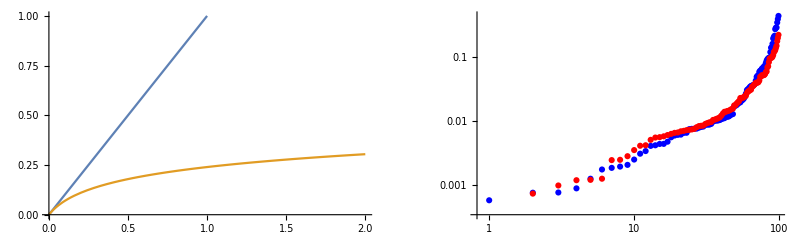

```mathematica
GraphicsRow[{Plot[{t,Log[1+10t]/10},{t,0,2},PlotRange->{{0,2},{0,1}}],Show[MapThread[ListLogLogPlot[#,PlotRange->All,PlotStyle->#2]&,{{RandomCoalescenceTimesG[100,0],RandomCoalescenceTimesG[100,10]},{Blue,Red}}]]}]
```

With a shrinking population, deeper coalescences may never occur: the ancestral population grows faster than lineages coalesce. t_crit=-1/λ, here giving an upper bound of t=0.1.

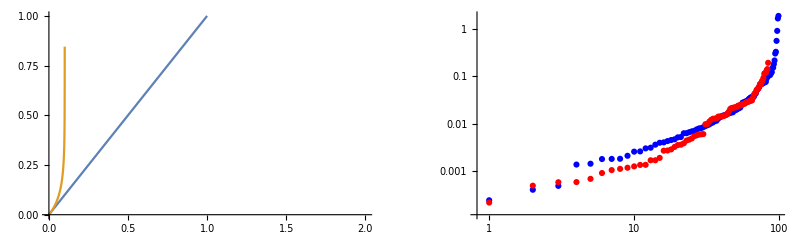

```mathematica
GraphicsRow[{Plot[{t,-Log[1-10t]/10},{t,0,2},PlotRange->{{0,2},{0,1}}],Show[MapThread[ListLogLogPlot[#,PlotRange->All,PlotStyle->#2]&,{{RandomCoalescenceTimesG[100,0],RandomCoalescenceTimesG[100,-10]},{Blue,Red}}]]}]
```

#### NumberOfCoalescences[k,T] gives a randomly sampled number of coalescence events that occur in T (scaled to 2N) NumberOfCoalescences[{t1,t2..}] does the same, for a given list of coalescence times.

```mathematica
NumberOfCoalescences[k_Integer,T_]:=NumberOfCoalescences[RandomCoalescenceTimes[k],T];
```

```mathematica
NumberOfCoalescences[tl_List,T_]:=Length[Select[tl,(#<T)&]];
```

#### TotalLength[{t1,t2,..}] is the total length of the tree

```mathematica
TotalLength[tl_List]:=Plus@@tl+Last[tl];
```

#### RandomFamilies[k] generates a list of the family sizes going back through time to the common ancestor of k genes.

```mathematica
RandomFamilies[k_Integer]:=NestList[RandomPreviousFamily,Array[1&,k],k-1];
```

#### RandomPreviousFamily[{1,1,2,3}] generates a random coalescence to give the previous family structure

```mathematica
RandomPreviousFamily[{k_Integer}]:={k};
RandomPreviousFamily[n_List]:=Module[{rp,k=Length[n],n2},
		(*rp=RandomSet[2,k];*)
rp=Sort[RandomSample[Range[k],2]];
n2=n⟦rp⟦2⟧⟧;Sort[ReplacePart[Delete[n,rp⟦2⟧],n2+n⟦rp⟦1⟧⟧,rp⟦1⟧]]];
```

#### RandomGenealogy[{leaf_1,leaf_2,…}] gives a random realisation of the coalescent process. Terminal nodes are labelled {leaf_1,leaf_2,…}, and internal nodes are labelled by an integer, in the order in which they occur. Each node carries its time, scaled to 2N generations. MutationRate→θ simulates infinite-sites mutation at a rate θ=4Nμ; mutations are labelled by unique integers. NodeLabels→{label_1,…} can be used to label internal nodes.

```mathematica
Options[RandomGenealogy]={NodeLabels->None,MutationRate->None,CoalescenceTimes->Random};
```

```mathematica
RandomGenealogy[ls_,opts___Rule]:=
	Module[{n=Length[ls],nl,li,ni,mu,μT,rt,rg,nm=0,j,λ},
		rt=CoalescenceTimes/.{opts}/.Options[RandomGenealogy];
             If[rt===Random,rt=RandomCoalescenceTimes[n]];
		nl=NodeLabels/.{opts}/.Options[RandomGenealogy];
		mu=MutationRate/.{opts}/.Options[RandomGenealogy];
		li=If[mu===None,Array[{0}&,n],Array[{0,μT}&,n]];
		ni=If[mu===None,(List/@rt),{#,μT}&/@rt];
		rg=FamilyToGenealogy[ls,RandomFamilies[n],NodeLabels->nl,NodeInformation->ni,LeafInformation->li];
	If[mu===None,
			rg,
		  rg⟦2⟧={rt⟦-1⟧,{}};
			rg//.{Node[i1_,{t1_,μ_List},{a___,Node[i2_,{t2_,μT},{m___}],b___}]:>
						(λ=mu(t1-t2)/2;
							j=If[λ==0,0,Random[PoissonDistribution[λ]]];
							nm=nm+j;Node[i1,{t1,μ},{a,Node[i2,{t2,Sort[Join[μ,Range[nm-j+1,nm]]]},{m}],b}])}]];
```

#### DeletedMutations[g,{T_0,T_1}] lists those mutations that should be deleted because they occurred in time interval {T_0,T_1}. This list may be to some extent randomly generated.

```mathematica
DeletedMutations[g_Node,{T0_,T1_}]:=Module[{tt={},ii,mi},((mi=MutationInterval[g,#1];ii=IntervalIntersection[Interval[{T0,T1}],Interval[mi]];If[!ii===Interval[],If[(Max[mi]-Min[mi]) RandomReal[]<Max[ii]-Min[ii],AppendTo[tt,#1]]])&)/@Mutations[g];tt];
```

#### RandomBottleneckedGenealogy[leaves,{T0,T1},θ] gives a random genealogy, with no mutations occurring in time interval {T0,T1}.

```mathematica
RandomBottleneckedGenealogy[lv_,{T0_,T1_},θ_]:=
	Module[{g=RandomGenealogy[lv,MutationRate->θ] ,dl},
	   dl=DeletedMutations[g,{T0,T1}];
		TransformInformation[g,ReplacePart[#2,Complement[#2⟦2⟧,dl],2]&]];
```

### Generating functions

#### MomentGeneratingFunction[g,ω,θ] gives the generating function for the number of mutations along each branch of the genealogy, under the infinite sites model.

```mathematica
MomentGeneratingFunction[Node[i_,_List,{Node[a_,s_List,{nn__Node}]}],ω_,θ_]:=
	MomentGeneratingFunction[Node[a,s,{nn}],ω,θ];
```

SetDelayed::write: Tag MomentGeneratingFunction in MomentGeneratingFunction[Node[i_,_List,{Node[a_,s_List,{nn__Node}]}],ω_,θ_] is Protected.

```mathematica
MomentGeneratingFunction[Node[i_,_List,{Node[a_,_List,{}],Node[b_,_List,{}]}],ω_,θ_]:=
	1/(1+θ(1-(ω[a]+ω[b])/2));
```

SetDelayed::write: Tag MomentGeneratingFunction in MomentGeneratingFunction[Node[i_,_List,{Node[a_,_List,{}],Node[b_,_List,{}]}],ω_,θ_] is Protected.

```mathematica
MomentGeneratingFunction[g_Node,ω_,θ_]:=Module[{
			leaves=Leaves[g],
		n,λ,ϕ},
		n=Length[leaves];λ=n/2(θ+n-1);ϕ=θ/(n(θ+n-1));
			1/(λ(1-ϕ(Plus@@(ω/@leaves))))*(Plus@@((MomentGeneratingFunction[g/.{Node[x_,y_,{Node[#⟦1⟧,_,{}],Node[#⟦2⟧,_,{}]}]:>Node[x,y,{}],Node[x_,y_,{Node[#⟦2⟧,_,{}],Node[#⟦1⟧,_,{}]}]:>Node[x,y,{}]},ω,θ])&/@SiblingList[g]))];
```

SetDelayed::write: Tag MomentGeneratingFunction in MomentGeneratingFunction[g_Node,ω_,θ_] is Protected.

```mathematica
MomentGeneratingFunction[{g__List},ω_,θ_]:=MomentGeneratingFunction[{g},ω,θ]=Module[{
		n=Length[{g}],λ,ϕ,ng,gl,i,j},
		If[n==1,1,λ=n/2(θ+n-1);ϕ=θ/(n(θ+n-1));
    gl=Flatten[Table[Sort[{{g}⟦i⟧,{g}⟦j⟧}],{i,2,n},{j,i-1}],1];
		1/(λ(1-ϕ(Plus@@(ω[Sort[#]]&/@{g}))))Plus@@((ng={g}/.{{x___,#⟦1⟧,y___,#⟦2⟧,z___}:>Sort[{x,Join[#⟦1⟧,#⟦2⟧],y,z}],{x___,#⟦2⟧,y___,#⟦1⟧,z___}:>Sort[{x,Join[#⟦1⟧,#⟦2⟧],y,z}]};MomentGeneratingFunction[ng,ω,θ])&/@gl)]];
```

SetDelayed::write: Tag MomentGeneratingFunction in MomentGeneratingFunction[{g__List},ω_,θ_] is Protected.

### The probability of genealogies

#### PossibleCoalescenceOrder[g] lists the possible orders in which coalescence events might occur; each is given by an ordered list of nodes.

```mathematica
PossibleCoalescenceOrder[Node[i_,_,{Node[a_,_,{}],Node[b_,_,{}]}]]:={Append[Sort[{a,b}],i]};
```

```mathematica
PossibleCoalescenceOrder[Node[i_,_,{Node[a_,s_,{nn__Node}]}]]:=Append[#,i]&/@PossibleCoalescenceOrder[Node[a,s,{nn}]];
```

```mathematica
PossibleCoalescenceOrder[g_Node]:=
	Module[{sl=SiblingList[g],tl={},lv,j},
		Do[tl=Join[tl,Join[sl⟦j⟧,#]&/@PossibleCoalescenceOrder[g/.{Node[i_,s_,{Node[sl⟦j,1⟧,_,{}],Node[sl⟦j,2⟧,_,{}]}]:>Node[i,s,{}],Node[i_,s_,{Node[sl⟦j,2⟧,_,{}],Node[sl⟦j,1⟧,_,{}]}]:>Node[i,s,{}]}]],{j,Length[sl]}];lv=Sort[Leaves[g]];
		Join[lv,TakeAway[#,lv]]&/@tl];
```

#### RandomCoalescenceOrder[g] gives a random ordering of the possible coalescence events

```mathematica
RandomCoalescenceOrder[Node[i_,_,{Node[a_,_,{}],Node[b_,_,{}]}]]:=Append[Sort[{a,b}],i];
```

```mathematica
RandomCoalescenceOrder[Node[i_,_,{Node[a_,s_,{nn__Node}]}]]:=Append[RandomCoalescenceOrder[Node[a,s,{nn}]],i];
```

```mathematica
RandomCoalescenceOrder[g_Node]:=Module[{sl=SiblingList[g],lv,j,tl},j=RandomInteger[{1,Length[sl]}];tl=Join[sl⟦j⟧,RandomCoalescenceOrder[g/.{Node[i_,s_,{Node[sl⟦j,1⟧,_,{}],Node[sl⟦j,2⟧,_,{}]}]:>Node[i,s,{}],Node[i_,s_,{Node[sl⟦j,2⟧,_,{}],Node[sl⟦j,1⟧,_,{}]}]:>Node[i,s,{}]}]];lv=Sort[Leaves[g]];Join[lv,TakeAway[tl,lv]];
```

#### NumberOfPossibleCoalescences[g,nodelist] gives the number of possible coalescences that could occur at each step. Only internal nodes are included. The order of coalescences is defined by nodelist

```mathematica
NumberOfPossibleCoalescences[g_Node,nl_]:=Module[{lv=Leaves[g],ng=g,tt={}},
       Scan[(AppendTo[tt,Length[SiblingList[ng]]];
			ng=ng/.Node[#,s_,{___}]:>Node[#,s,{}])&,TakeAway[nl,lv]];tt];
```

#### IncidenceMatrix[g,nodelist] gives the matrix describing an ordering of coalescences defined by nodelist. The last member of nodelist is the root node. The elements of the matrix show whether a branch is present during the time for which there are 1≤i≤n lineages. Rows correspond to branches, in the order specified by nodelist.

```mathematica
Unprotect[IncidenceMatrix];
```

```mathematica
IncidenceMatrix[g_Node,nl_List] :=Module[{
			leaves=Leaves[g],
			n=NumberOfLineages[g],S={If[FreeQ[g, Node[#,_,{}]],0,1]&/@nl},x,i},
		 Do[PrependTo[S,First[S]];
	         S⟦1,i⟧=1;x=(Position[nl,#]⟦1,1⟧&/@Descendants[g,nl⟦i⟧]);
			    S⟦1,x⟦1⟧⟧=0;S⟦1,x⟦2⟧⟧=0;,{i,n+1,2n-1}];
Transpose[S]];
```

```mathematica
Protect[IncidenceMatrix];
```

#### MonteCarloProbability[g,nodelist,J,θ,ns] makes a Monte Carlo estimate of the probability of the genealogy g and the mutational configuration J, assuming that the coalescences are in the order specified by nodelist. A list of ns values is returned. MonteCarloProbability[g,J,θ,ns] makes no assumptions as to the order of events.

```mathematica
MonteCarloProbability[Node[i_,_,{g_Node}],nl_List,J_List,θ_,ϕ_,ns_Integer] :=
	Module[{ps=Position[nl,i]⟦1,1⟧},
		MonteCarloProbability[g,Delete[nl,ps],Delete[ J,ps],θ,ϕ,ns]];
```

```mathematica
MonteCarloProbability[g_Node,nl_List,J_List,θ_,θ1_,ns_Integer] :=Module[{n=NumberOfLineages[g],S=IncidenceMatrix[g,nl],i,j,ϕv,ϕv1,ϕ,ϕ1,λ,Jt},
		ϕ=Table[θ/(i(θ+i-1)),{i,1,n}];ϕv=(#.ϕ1)&/@S;
		ϕ1=Table[θ1/(i(θ1+i-1)),{i,1,n}];ϕv1=(#.ϕ1)&/@S;
		λ=∏_(i=2)^n (i/2 (θ+i-1));
 ((Times@@MapThread[Power,{ϕv,J}])/(λ(Times@@(Factorial/@J) )))*Table[
				Jt=Plus@@MapThread[RandomMultinomial[#3,(#1ϕ1)/#2]&,{S,ϕv1,J}];
				Times@@MapThread[(#1!(#2/#3)^#1)&,{Jt,ϕ,ϕ1}],{ns}]];
```

```mathematica
MonteCarloProbability[g_Node,J_List,θ_,θ1_,ns_Integer] :=
	Module[{nl=RandomCoalescenceOrder[g]},
		MonteCarloProbability[g,nl,J,θ,θ1,ns]*(Times@@Drop[NumberOfPossibleCoalescences[g,nl],-1])];
```

#### NumberOfMutations[g,node] gives the number of mutations that occurred on the branch leading down to the specified node. The set of mutations is given in the second element of the information for each node.

```mathematica
Options[NumberOfMutations]={NodeFunction->(#2⟦2⟧&)};
```

```mathematica
NumberOfMutations[g_Node,i_,opts___Rule]:=
	Module[{a=Ancestors[g,i],	nf=NodeFunction/.{opts}/.Options[NumberOfMutations]},
		If[a==={},
			0,
			Length[
				Complement[
					nf[i,ExtractInformation[g,i]],
					nf[Last[a],ExtractInformation[g,Last[a]]]]]]];
```

#### Mutations[g] gives the set of mutations that occurred on g. Mutations[g,i] gives the mutations that arose on the branch leading down to node i. By default, these are held in the second element of the information list. NodeFunction→f uses f[i,info] to extract the mutation list.

```mathematica
Options[Mutations]={NodeFunction->(#2⟦2⟧&)};
```

```mathematica
Mutations[g_Node,opts___Rule]:=Module[{nf=NodeFunction/.{opts}/.Options[Mutations]},
		Union[Flatten[CollapseGenealogy[g,NodeFunction->nf]⟦2⟧]]]
```

```mathematica
Mutations[g_Node,i_,opts___Rule]:=Module[{nf=NodeFunction/.{opts}/.Options[Mutations],an=Ancestors[g,i]},
		Complement[nf[i,ExtractInformation[g,i]],If[an==={},{},nf[Last[an],ExtractInformation[g,Last[an ]]]]]]
```

#### MutationOrigin[g,k] gives the first node at which mutation k appears.

```mathematica
Options[MutationOrigin]={NodeFunction->(Take[#2,2]&)};
```

```mathematica
MutationOrigin[g_Node,k_,opts___Rule] :=Module[{ll,nf=NodeFunction/.{opts}/.Options[MutationOrigin]},
		ll=CollapseGenealogy[g,NodeFunction->(If[MemberQ[nf[#1,#2]⟦2⟧,k],{nf[#1,#2]⟦1⟧,#1},{-∞,#1}]&),Nested->False];
		ll=First[Sort[ll,(#1⟦1⟧>#2⟦1⟧)&]];
		If[ll⟦1⟧===-∞,$Failed,ll⟦2⟧]];
```

#### MutationInterval[g,k,t] gives the time .interval in which mutation k arose.

```mathematica
Options[MutationInterval]={NodeFunction->(Take[#2,2]&)};
```

```mathematica
MutationInterval[g_Node,k_,opts___Rule]:=Module[{nn=MutationOrigin[g,k,opts],an,t0,t1,nf=NodeFunction/.{opts}/.Options[MutationInterval]},
	If[nn===$Failed,$Failed,
			t0=nf[nn,ExtractInformation[g,nn]]⟦1⟧;
			an=Ancestors[g,nn];
			If[an==={},{t0,∞},
			t1=nf[Last[an],ExtractInformation[g,Last[an]]]⟦1⟧;
			{t0,t1}]]];
```

#### ExactProbability[g,θ] gives the probability of this genealogy, given a scaled mutation rate θ=4Nμ. By default, the number of mutations is deduced from a list of unique mutations held in the second element of the information list. NodeFunction→f uses f[i,info] to find the number of mutations. Uses MomentGeneratingFunction[], and so is intractable for large numbers of mutations and for large genealogies. ExactProbability[S,θ] uses the generating function over all topologies to find the net probability of the configuration of mutations represented by the matrix S.

```mathematica
Options[ExactProbability]={NodeFunction->(#2⟦2⟧&)};
```

```mathematica
ExactProbability[g_Node,θ_,opts___Rule]:=Module[{ω,mgf,jl,
			nl=Nodes[g],
			nf=NodeFunction/.{opts}/.Options[ExactProbability]},
		mgf=MomentGeneratingFunction[g,ω,θ];
	  jl=NumberOfMutations[g,#]&/@nl;
	  jl=Reverse/@Sort[Transpose[{jl,ω/@nl}]];
		Scan[(mgf=D[mgf,#]/(#⟦2⟧!)/.#⟦1⟧->0)&,jl];mgf//Factor];
```

```mathematica
ExactProbability[S_List,θ_]:=Module[{ω,ν,mgf,jl,rl,ll,nl=Length[S],nm=Length[S⟦1⟧],ff=Reverse[Sort[Tally[Transpose[S]]],2]},ll=List/@Range[nl];mgf=MomentGeneratingFunction[ll,ω,θ];Factor[If[0==Plus@@Plus@@S,mgf/.ω[_]:>0,jl=ff/.{i_Integer,s_List}:>{i,ν@@(Extract[ll,#1]&)/@Position[s,1]}/.ν[a__List]:>ν[Flatten[{a}]];jl=Reverse/@Sort[jl];rl=jl/.{{ν[a_],_}:>ω[a]->ν[a]};mgf=mgf/.rl/.ω[_]:>0;Scan[(mgf=D[mgf, #1]/(#1⟦2⟧!)/.#1⟦1⟧->0)&,jl];mgf]]];
```

#### GenealogyToMatrix[g] gives a matrix whose rows specify which mutations are found in which leaf of the genealogy. By default, the list of mutations is taken from the second element of the information list. NodeFunction→f uses f[i,info] to specify the mutations in each node.

```mathematica
Options[GenealogyToMatrix]={NodeFunction->(#2⟦2⟧&)};
```

```mathematica
GenealogyToMatrix[g:Node[_,_List,_List]|{Node[_,_List,_List]...},opts___Rule]:=ListToMatrix[CollapseGenealogy[g,Nested->False,Node->False,NodeFunction->(NodeFunction/.{opts}/.Options[GenealogyToMatrix])],opts];
```

#### MatrixToGenealogy[S,{leaf_1, leaf_2,…},{μ_1,…}] constructs a genealogy from the matrix S. The leaves are labelled by {leaf_1, …} and the mutations by {μ_1,…}; internal nodes are labelled by unique integers

```mathematica
Options[MatrixToGenealogy]={Unrooted->False};
```

```mathematica
MatrixToGenealogy[S_List,ll_List,ml_List,opts___Rule]:=
If[ValidMatrixQ[S,opts],
If[Unrooted/.{opts}/.Options[MatrixToGenealogy],
MatrixToUnrootedGenealogy[S,ll,ml],
MatrixToRootedGenealogy[S,ll,ml]],
Message[MatrixToGenealogy::invalidMatrix,S];$Failed];
```

```mathematica
MatrixToRootedGenealogy[S_List,ll_List,ml_List]:=Module[{nl=Length[S],j,g,rtn,sharedMutations,nodeCount,lS=MatrixToList[S,MutationLabels->ml]},
	sharedMutations=Extract[ml,#]&/@Position[Transpose[S],{(1)..}];
	nodeCount=2;
	g=Node[1,{0,sharedMutations},{Node[ll⟦1⟧,{0,lS⟦1⟧},{}]}];
	Do[rtn=FindNode[g,lS⟦j⟧,nodeCount];
			  If[rtn===$Failed,
				g=$Failed;Break[],
				If[!(rtn⟦1⟧===rtn⟦2⟧),nodeCount+=1];
				 g=AddGenealogy[g,Node[ll⟦j⟧,{0,lS⟦j⟧},{}],rtn⟦1⟧,rtn⟦2⟧,{0,rtn⟦3⟧}]],
			{j,2,nl}];
		g];
```

```mathematica
MatrixToGenealogy::invalidMatrix="The matrix `1` is not consistent with any genealogy";
```

```mathematica
MatrixToGenealogy::multipleSplit="Mutation `1` appears to split the genealogy at several nodes.  The list of possible nodes, and the current genealogy are `2`, `3`";
```

```mathematica
MatrixToUnrootedGenealogy[S_List,ll_List,ml_List]:=
Module[{nl,mlist,j,nleaves=Length[S],nmutns=Length[S⟦1⟧],rs,rs2,vms,nn=1,ms1,ms2,mm},
nl=Append[Node[#,{0,{}},{1}]&/@ll,Node[nn,{0,{}},ll]];
mlist=MatrixToList[S,MutationLabels->ml];
llist=MatrixToList[Transpose[S],MutationLabels->ll];
vms=ml⟦#⟧&/@Select[Range[nmutns],Length[llist⟦#⟧]>1&];
nl=AddMutation[1,vms,AddMutation[ll,mlist,nl]];
Do[If[1<Length[llist⟦j⟧]<nleaves-1,
(*Print["Doing mutation",j];*)
nds=Cases[nl,Node[_,{_,{___,ml⟦j⟧,___}},{_,_,__}]];
(*Print["nds=",nds];*)
rs=nds/.{Node[nd_,_,rs_]:>(rs2=Select[rs,MemberQ[ExtractInformation[nl,#]⟦2⟧,ml⟦j⟧]&];
{nd,rs2,Complement[rs,rs2]})};
(*Print["rs=",rs];*)
rs=Select[rs,(1<Length[#⟦2⟧]&&1<Length[#⟦3⟧])&];
(*Print["rs=",rs];*)
If[Length[rs]>1,Message[MatrixToGenealogy::multipleSplit,ml⟦j⟧,rs,nl]];
If[Length[rs]>0,
(rs=First[rs];
(*Print["Split at ",rs];*)
nn+=1;mm=ExtractInformation[nl,rs⟦1⟧]⟦2⟧;
nl=nl/.Node[rs⟦1⟧,_,_]:>(ms1=Union[Flatten[ExtractInformation[nl,#]⟦2⟧&/@rs⟦2⟧]];
Node[rs⟦1⟧,{0,Intersection[ms1,mm]},Append[rs⟦2⟧,nn]]);
AppendTo[nl,ms2=Union[Flatten[ExtractInformation[nl,#]⟦2⟧&/@rs⟦3⟧]];
Node[nn,{0,Intersection[ms2,mm]},Append[rs⟦3⟧,rs⟦1⟧]]];
((nl=nl/.Node[#,x_,y_]:>Node[#,x,y/.rs⟦1⟧:>nn])&/@rs⟦3⟧);)]],
{j,Length[ml]}];
nl];
```

#### FindNode[g,{m_1,…},newNode] finds from where in the genealogy g a leaf carrying mutations {m_1,…} descends. If no node or branch matches, returns $Failed. If the leaf joins the branch above node i, returns {i,newNode,{m_1,…}}, where newNode is a new node label, distinct from any other in g. The last element lists the mutations carried at the new node. If the leaf joins at node i, returns {i,i,{m_1,…}}, where the last element lists the mutations carried at node i. The new leaf MUST contain all the mutations in the root node of g.

```mathematica
FindNode[g_Node,leafMutations_List,newNode_]:=
	Module[{nd=g⟦1⟧,oldNd=g⟦1⟧,desc,nodeMutations,descendantMutations,sharedMutations,lsm,ps,rtn={}},
		While[rtn==={},
		  desc=Descendants[g,nd];
       nodeMutations=ExtractInformation[g,nd]⟦2⟧;
       descendantMutations=Complement[#,nodeMutations]&/@(ExtractInformation[g,#]⟦2⟧&/@desc);
       sharedMutations=Intersection[#,leafMutations]&/@descendantMutations;
      lsm=Length/@sharedMutations;
      If[Complement[nodeMutations,leafMutations]==={},
	     If[Max[lsm]==0,
	        rtn={nd,nd,nodeMutations},
	        If[Max[lsm]!=Plus@@lsm,
		          If[Max[lsm]==-∞,
							rtn={nd,newNode,Intersection[leafMutations,nodeMutations]},
							Print["New leaf",leafMutations,"contains mutations from several branches:",lsm];
		         rtn=$Failed],
		         ps=Position[lsm,Max[lsm]]⟦1,1⟧;
		        If[Complement[descendantMutations⟦ps⟧,leafMutations]==={},
			          nd=desc⟦ps⟧,
			         rtn={desc⟦ps⟧,newNode,Join[nodeMutations,Intersection[leafMutations,descendantMutations⟦ps⟧]]}]]],
	Print["New leaf",leafMutations,"does not contain all mutations in node ",nd];
	rtn=$Failed]];
	rtn];
```

Choose a node at the top
If new leaf does not contain all mutations at the node and none of the new descendant mutations,then
	if that node is a leaf, make a new node just above; otherwise join the node.
else if new leaf contains some new mutations from several descendant branches, FAIL
 	else if contains ALL mutations from ONE branch, move down & repeat
 		else attach to that branch

#### MatrixToList[S] converts a matrix representation to a list of the mutations held by each leaf. By default, mutations are numbered 1,2…. MutationLabels→{m_1,…} uses the specified labels.

```mathematica
Options[MatrixToList]={MutationLabels->Automatic};
```

```mathematica
MatrixToList[S_List,opts___Rule] :=Module[{i,nl=Length[S],nm=Length[S⟦1⟧],ml},
			ml=MutationLabels/.{opts}/.Options[MatrixToList];
		  If[ml===Automatic,ml=Range[nm]];
		  Table[Extract[ml,#]&/@Position[S⟦i⟧,1],{i,nl}]];
```

#### ListToMatrix[{{1,2,3},{4},…}] converts a list of mutations present at each node into a matrix representation. MutationLabels→{m_1,…} gives the columns in the specified order.

```mathematica
Options[ListToMatrix]={MutationLabels->Automatic};
```

```mathematica
ListToMatrix[z_List,opts___Rule] :=
	Module[{i,nl=Length[z],zl=Union[Flatten[z]]},
			ml=MutationLabels/.{opts}/.Options[MatrixToList];
		  If[ml===Automatic,ml=zl];
		  Table[If[MemberQ[z⟦i⟧,#],1,0]&/@ml,{i,nl}]];
```

#### GriffithsTavare[S,θ] uses the Griffiths-Tavare algorithm to find the probability of a configuration of mutations defined by the matrix S.

```mathematica
GriffithsTavare[{},θ_]:=GriffithsTavareFailed[{}];
```

```mathematica
GriffithsTavare[{g1_List,g2_List},θ_]:=
	GriffithsTavare[{g1,g2},θ]=
		Module[{a1=Plus@@(g1(1-g2)),a2=Plus@@(g2(1-g1))},
		Binomial[a1+a2,a1](θ/(2(1+θ)))^(a1+a2)1/(1+θ)];
```

```mathematica
GriffithsTavare[S_List,θ_]:=If[OrderedQ[S]&&OrderedQ[Transpose[S]],GriffithsTavare[S,θ]=Module[{λ,ps,dt,ff=DeleteCases[Reverse[Sort[Tally[S]],2],{1,_}],n=Length[S],nm=Length[S⟦1⟧],mutationTerms,coalescenceTerms},ps=Position[Plus@@S,1];mutationTerms=If[Length[ps]==0,0,If[nm==1,GriffithsTavare[S/.{1->0},θ],dt=Union[(Transpose[Delete[Transpose[S],#1⟦1⟧]]&)/@ps];Plus@@(GriffithsTavare[#1,θ]&)/@dt]];coalescenceTerms=If[ff==={},0,ff=Transpose[ff];If[Max[First[ff]]≤1,0,Plus@@MapThread[1/2 (#1 (#1-1)) GriffithsTavare[Delete[S,Position[S,#2]⟦1,1⟧],θ]&,ff]]];λ=1/2 n (θ+n-1);Factor[((θ mutationTerms)/2+coalescenceTerms)/λ]],GriffithsTavare[Transpose[Sort[Transpose[Sort[S]]]],θ]];
```

The time taken increases dramatically with the # of genes: for 6 genes, 1.8s, for 7 genes too long to wait.  (Though, these timings are somewhat random). Presumably Wu (2010) algorithm would be faster.

```mathematica
rg=RandomGenealogy[Array[Subscript[x, #]&,7],MutationRate->50];
mm=GenealogyToMatrix[rg];
Timing[eq=GriffithsTavare[mm,θ];]
```

$Aborted

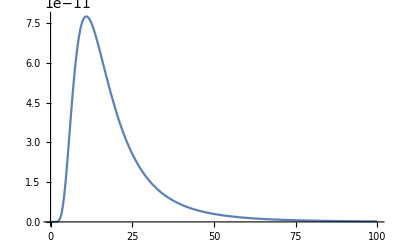

```mathematica
Plot[eq//N,{θ,0,30}]
```

#### MonteCarloGriffithsTavare[S,θ] uses the Monte-Carlo Griffiths-Tavare algorithm to find the probability of a configuration of mutations defined by the matrix S.

```mathematica
MonteCarloGriffithsTavare[S_List,θ_,ϕ_]:=Module[{pr=1,nS=S,n,ps,J,K,nm=Length[S⟦1⟧]},While[!nS==={{0}},st=Transpose[nS];ust=Union[st];ps=Position[Plus@@Transpose[ust],1];J=Length[ps];ff=DeleteCases[Reverse[Sort[Tally[nS]],2],{1,_}];K=If[ff==={},0,fft=Transpose[ff];If[Max[First[fft]]≤1,0,1/2 fft⟦1⟧.(fft⟦1⟧-1)]];n=Length[nS];nS=If[RandomReal[]<(J ϕ)/(J ϕ+2 K),If[Length[nS⟦1⟧]==1,nS/.{1->0},rj=ps⟦RandomInteger[{1,J}],1⟧;Transpose[Delete[st,Position[st,ust⟦rj⟧]⟦1,1⟧]]],rk=RandomList[1,(fft⟦1⟧ (fft⟦1⟧-1))/(2 K)];Delete[nS,Position[nS,fft⟦2,1⟧]⟦1,1⟧]];pr*=(J ϕ+2 K)/(n (θ+n-1))];pr (θ/ϕ)^nm];
```

```mathematica
MonteCarloGriffithsTavare[S_List,θ_]:=MonteCarloGriffithsTavare[S,θ,θ];
```

#### ValidMatrixQ

```mathematica
ValidMatrixQ::notTensor="ValidMatrixQ[`1`] should have as an argument a tensor of rank 2, containing 0 or 1";
```

```mathematica
Options[ValidMatrixQ]={Unrooted-> False};
```

```mathematica
ValidMatrixQ[S:{{(0|1)...}...},opts___Rule]:=Module[{tS},
If[MatrixQ[S],
If[Dimensions[S]⟦-1⟧<2,
True,
tS=Union[Transpose[S]];
If[Unrooted/.{opts}/.Options[ValidMatrixQ],
Max[ValidMatrixQ[0,0][tS]ValidMatrixQ[1,0][tS]ValidMatrixQ[0,1][tS]ValidMatrixQ[1,1][tS]]==0,
Max[ValidMatrixQ[1,0][tS]ValidMatrixQ[0,1][tS]ValidMatrixQ[1,1][tS]]==0]],
Message[ValidMatrixQ::notTensor,S]]];
```

```mathematica
ValidMatrixQ[1,1]=Compile[{{tS,_Integer,2}},
1-(Times@@Transpose[1-Outer[Times,tS,tS,1],{3,2,1}])];
ValidMatrixQ[0,1]=Compile[{{tS,_Integer,2}},
1-(Times@@Transpose[1-Outer[Times,1-tS,tS,1],{3,2,1}])];
ValidMatrixQ[1,0]=Compile[{{tS,_Integer,2}},
1-(Times@@Transpose[1-Outer[Times,tS,1-tS,1],{3,2,1}])];
ValidMatrixQ[0,0]=Compile[{{tS,_Integer,2}},
1-(Times@@Transpose[1-Outer[Times,1-tS,1-tS,1],{3,2,1}])];
```

#### SwapStates

```mathematica
SwapStates[s:{(0|1)...},S:{{(0|1)...}...}]:=(s+#(1-2s))&/@S;
```

#### MissingCombination

```mathematica
MissingCombination::invalidMatrix="The matrix is not consistent with any genealogy: `1`";
```

```mathematica
MissingCombination[S:{{(0|1)...}...}]:=MissingCombination[S]=
Module[{ut,tS=Transpose[S]},
Outer[(ut=Union[Transpose[{##}]];
Switch[Length[ut],
4,Message[MissingCombination::invalidMatrix,S];$Failed,
3,Complement[{{0,0},{0,1},{1,0},{1,1}},ut]//First,
_,{}])&,tS,tS,1]];
```

#### PossibleRootings

```mathematica
PossibleRootings[x_?((ListQ[#]&&FreeQ[#, Null])&),S:{{(0|1|Null)...}...}]:=x;
PossibleRootings[{a___List,{c___,Null,d___},b___List},S:{{(0|1|Null)...}...}]:=
Module[{i,α,β,nl=Length[S],nm=Length[S⟦1⟧],
tS=Transpose[S],miss,ut,j=Length[{c}]+1,cd={c,Null,d},t0,t1,t0Q=True,t1Q=True},
miss=Transpose[MissingCombination[S]]⟦j⟧;
t0=Table[If[α==j,
0,
Switch[cd⟦α⟧,
Null,Switch[miss⟦α⟧,
{0,0},1,
{1,0},0,
_,Null],
0,If[miss⟦α⟧=={0,0},t0Q=False];0,
1,If[miss⟦α⟧=={1,0},t0Q=False];1]],{α,nm}];
t1=Table[If[α==j,
1,
Switch[cd⟦α⟧,
Null,Switch[miss⟦α⟧,
{0,1},1,
{1,1},0,
_,Null],
0,If[miss⟦α⟧=={0,1},t1Q=False];0,
1,If[miss⟦α⟧=={1,1},t1Q=False];1]],{α,nm}];
If[t0Q,If[t1Q,{a,t0,t1,b},{a,t0,b}],If[t1Q,{a,t1,b},{a,b}]]];
```

```mathematica
PossibleRootings[S:{{(0|1|Null)...}...}]:=FixedPoint[PossibleRootings[#,S]&,{Array[Null&,{Length[S⟦1⟧]}]}];
```

#### AddMutation

```mathematica
AddMutation::invalidLists="The lists of nodes `1` and of mutations `2` are not compatible.";
```

```mathematica
AddMutation[n_,m_?(Not[ListQ[#]]&),g:(Node[_,_List,{___Node}]|{Node[_,_List,_List]...})]:=
g/.Node[n,{x_,y_List,z___},d_List]:>Node[n,{x,Append[y,m],z},d];AddMutation[n_,m_List,g:(Node[_,_List,{___Node}]|{Node[_,_List,_List]...})]:=
g/.Node[n,{x_,y_List,z___},d_List]:>Node[n,{x,Join[y,m],z},d];
```

This is commented out, because I need to be able to represent nodes as lists - which the old version would not allow.

```mathematica
(*AddMutation[n_List,m_List,g:(Node[_,_List,{___Node}]|{Node[_,_List,_List]...})]:=
If[Length[n]==Length[m],
Fold[AddMutation[#2⟦1⟧,#2⟦2⟧,#1]&,g,Transpose[{n,m}]],
Message[AddMutation::invalidLists,n,m]];*)
```

#### CondenseMatrix

```mathematica
Options[CondenseMatrix]={Unrooted->False};
```

```mathematica
CondenseMatrix::notMatrix="`1` is not a matrix";
```

```mathematica
CondenseMatrix[S:{{(0|1)...}...},opts___Rule]:=If[MatrixQ[S],
Module[{tSR},
If[Unrooted/.{opts}/.Options[CondenseMatrix],
tSR=DeleteCases[Union[Transpose[S]],{0 ...}|{1 ...}|{0 ... ,1,0 ...}|{1 ... ,0,1 ...}];
Transpose[Union[tSR/.{x:{(0|1)...}:>First[Sort[{x,1-x}]]}]],
Transpose[DeleteCases[Union[Transpose[S]],{0 ...}|{1 ...}|{0 ... ,1,0 ...}]]]],
Message[CondenseMatrix::notMatrix,S]];
```

### Recombination

#### AncestralGraphPattern

```mathematica
AncestralGraphPattern={AncestralLineagePattern...};
```

#### AncestralLineagePattern

```mathematica
AncestralLineagePattern=AncestralLineage[_,{_,_},_List,_List,{___List}];
```

#### Junctions

```mathematica
Junctions[AncestralLineage[_,{_,_},_List,j_List,_List]]:=Drop[j,-1];
Junctions[g:AncestralGraphPattern]:=Union[Flatten[Junctions/@g]];
```

#### MapLength

```mathematica
MapLength::mixedLengths="The map lengths `1` differ among lineages";
```

```mathematica
MapLength[AncestralLineage[_,{_,_},_List,j_List,_List]]:=Last[j];
MapLength[g:AncestralGraphPattern]:=
Module[{ml=Union[MapLength/@g]},
If[Length[ml]>1,
Message[MapLength::mixedLengths,ml]];
ml⟦1⟧];
```

#### TimesOfEvents

```mathematica
TimesOfEvents[g:AncestralGraphPattern]:=Union[Flatten[g/.AncestralLineage[_,{t0_,t1_},_List,_List,_List]:>{t0,t1}]];
```

#### AllEvents

```mathematica
AllEvents::badJunctions="The junctions at the recombination event at t=`1` in graph `2` do not change by 1.";
```

```mathematica
AllEvents::badRelationship="The event at t=`1` in graph `2` does not have the right form.";
```

```mathematica
AllEvents[g:AncestralGraphPattern]:=AllEvents[g]=Module[{cs,ce,jj},
(cs=Cases[g,AncestralLineage[_,{#,_},_List,_List,_List]];
ce=Cases[g,AncestralLineage[_,{_,#},_List,_List,_List]];
Switch[Length/@{ce,cs},
{0,_}|{_,0}|{2,1},
{#,ce/.ExtractLabel,cs/.ExtractLabel,None},
{1,2},
jj=TakeAway[Join[cs⟦1,4⟧,cs⟦2,4⟧],ce⟦1,4⟧];
(*If[!(MatchQ[jj,{x_,x_,1}]||(Sort[{cs⟦1,3⟧,cs⟦2,3⟧}]===Sort[{{{}},ce⟦1,3⟧}])),Message[AllEvents::"badJunctions",#1,g]]*)(* too hard to do *)
If[Not[{}===Cases[Transpose[{cs⟦2,4⟧,cs⟦2,3⟧}],{jj⟦1⟧,_}]⟦1,2⟧],
cs=Reverse[cs]];
{#,ce/.ExtractLabel,cs/.ExtractLabel,jj⟦1⟧},
_,
Message[AllEvents::badRelationship,#,g];
{#,ce/.ExtractLabel,cs/.ExtractLabel,None}])&/@TimesOfEvents[g]];
```

#### CoalescenceEvents

```mathematica
CoalescenceEvents[g:AncestralGraphPattern]:=Cases[AllEvents[g],{_,{_,_},{_},_}];
```

#### RecombinationEvents

```mathematica
RecombinationEvents[g:AncestralGraphPattern]:=RecombinationEvents[g]=Cases[AllEvents[g],{_,{_},{_,_},_}];
```

#### NullRecombinationEvents

```mathematica
NullRecombinationEvents[g:AncestralGraphPattern]:=NullRecombinationEvents[g]=Cases[AllEvents[g],{_,{_},{_,_},MapLength[g]}];
```

#### LeafEvents

```mathematica
LeafEvents[g:AncestralGraphPattern]:=LeafEvents[g]=Cases[AllEvents[g],{_,{},{__},_}];
```

#### RootEvents

```mathematica
RootEvents[g:AncestralGraphPattern]:=RootEvents[g]=Cases[AllEvents[g],{_,{__},{},_}];
```

#### Leaves

```mathematica
Leaves::multipleLineages="Some leaves share the same label: `1`";
```

```mathematica
Leaves[g:AncestralGraphPattern]:=
Module[{ss=Flatten[#⟦3⟧&/@LeafEvents[g]],uss,res},
uss=Union[ss];res=TakeAway[ss,uss]==={};
If[Not[res],Message[Leaves::multipleLineages,g]];
uss];
```

#### LineagesPresent

```mathematica
LineagesPresent[g:AncestralGraphPattern,t_]:=
Select[g,(#⟦2,1⟧≤t<#⟦2,2⟧)&]/.ExtractLabel;
LineagesPresent[g:AncestralGraphPattern]:=
g/.ExtractLabel;
```

#### RecombinantLineages

```mathematica
RecombinantLineages::multipleLineages="Some recombinant lineages share the same label: `1`";
```

```mathematica
RecombinantLineages[g:AncestralGraphPattern]:=
Module[{ss=Flatten[#⟦3⟧&/@RecombinationEvents[g]],uss,dss},
uss=Union[ss];dss=TakeAway[ss,uss];
If[Not[dss==={}],Message[RecombinantLineages::multipleLineages,g]];
uss];
```

#### CoalescentLineages

```mathematica
CoalescentLineages::multipleLineages="Some coalescent lineages share the same label: `1`";
```

```mathematica
CoalescentLineages[g:AncestralGraphPattern]:=
Module[{ss=Flatten[#⟦3⟧&/@CoalescenceEvents[g]],uss,dss},
uss=Union[ss];dss=TakeAway[ss,uss];
If[Not[dss==={}],Message[CoalescentLineages::multipleLineages,g]];
uss];
```

#### RootLineages

```mathematica
RootLineages::multipleLineages="Some root lineages share the same label: `1`";
```

```mathematica
RootLineages[g:AncestralGraphPattern]:=
Module[{ss=Flatten[(#⟦2⟧)&/@RootEvents[g]],uss,res},
uss=Union[ss];TakeAway[s,uss]==={};
If[Not[res],Message[RootLineages::multipleLineages,g]];
uss];
```

#### NullLineages

```mathematica
NullLineages[g:AncestralGraphPattern]:=NullLineages[g]=Cases[g,AncestralLineage[_,{_,_},{{}},{MapLength[g]},_List]];
```

#### TimespanOfLineage

```mathematica
TimespanOfLineage[g:AncestralGraphPattern,l_]:=ExtractLineage[g,l]⟦2⟧;
```

#### TimeSpanOfJunctions

```mathematica
TimespanOfJunction[ag:AncestralGraphPattern,j_]:=Module[{cc},
cc=Cases[ag,AncestralLineage[_,{_,_},_,{___,j,___},_]];
{First[Sort[cc/.AncestralLineage[_,{t0_,_},_,_,_]:>t0]],Last[Sort[cc/.AncestralLineage[_,{_,t1_},_,_,_]:>t1]]}];
```

#### ExtractLabel

```mathematica
ExtractLabel={AncestralLineage[l_,{_,_},_List,_List,_List]:>l};
```

#### ExtractInformation

```mathematica
ExtractInformation[g:AncestralGraphPattern,l_]:=Last[ExtractLineage[g,l]];
```

#### ExtractLineage

```mathematica
ExtractLineage::notPresent="Lineage `1` is not present in the graph `2`";
```

```mathematica
ExtractLineage::multipleLineages="Lineage `1` occurs more than once in the graph `2`";
```

```mathematica
ExtractLineage[g:AncestralGraphPattern,l_List]:=Map[ExtractLineage[g,#]&,l,1];
```

```mathematica
ExtractLineage[g:AncestralGraphPattern,l_?(Not[ListQ[#]]&)]:=Module[{cs},
cs=Cases[g,AncestralLineage[l,{_,_},_List,_List,_List]];
Switch[Length[cs],
0,Message[ExtractLineage::notPresent,l,g];{},
1,cs⟦1⟧,
_,Message[ExtractLineage::multipleLineages,l,g];cs]];
```

#### ExtractLineagesEndingAtT

```mathematica
ExtractLineagesEndingAtT[g:AncestralGraphPattern,t_]:=Module[{cs},
cs=Cases[g,AncestralLineage[_,{_,t},_List,_List,_List]]/.ExtractLabel];
```

#### ExtractLineagesStartingAtT

```mathematica
ExtractLineagesStartingAtT[g:AncestralGraphPattern,t_]:=Module[{cs},
cs=Cases[g,AncestralLineage[_,{t,_},_List,_List,_List]]/.ExtractLabel];
```

#### ExtractGenealogy

```mathematica
ExtractGenealogy::multipleRoots="Some of the leaves `1` have more than one ancestral lineage at map position `3`: `2`";
```

```mathematica
ExtractGenealogy[g:AncestralGraphPattern,x_]:=
Module[{ng=g,ds,ll=Leaves[g],rl},
rl=Union[Ancestors[g,#,AncestorList->Roots,MapPosition->x]&/@ll];
If[Length[rl]==1,
ds=Descendants[g,rl⟦1⟧,MapPosition->x,DescendantList->All];
ds=ds//.{a___,{l_?(Not[MemberQ[ll, #]]&),{}},b___}:>{a,b};
ListToGenealogy[ds,
NodeFunction->({First[TimespanOfLineage[g,#]]}&)],
Message[ExtractGenealogy::multipleRoots,ll,rl,x];$Failed]];
```

```mathematica
(* This is an old piece of code which is in some ways more efficient*)
(*
ExtractGenealogy[g:AncestralGraphPattern,x_]:=
Module[{ng=g,ds,ll=Leaves[g],rl},
rl=Union[Flatten[Ancestors[g,#,AncestorList->Roots]]]&/@ll;
If[And@@(Length[#]==1&/@rl),
ds=RecombinationEvents[g]/.{_,_,{aL_,aR_},j_}:>If[x<j,aR,aL];
(ng=DeleteCases[ng,AncestralLineage[#,{_,_},_List,_List,_List]])&/@ds;
ng,
Message[ExtractGenealogy::multipleRoots,ll,rl];$Failed]];
*)
```

```mathematica
ExtractGenealogy[g:AncestralGraphPattern]:=Module[{js=Junctions[g]},
ExtractGenealogy[g,#]&/@((Prepend[js,0]+Append[js,1])/2)];
```

```mathematica
Ancestors[ag,a]
```

{3}

#### Descendants

```mathematica
Options[Descendants]=Append[Options[Descendants],MapPosition->None];
```

```mathematica
Descendants::multipleLineages="Several events occur at `1`; `2`";
```

```mathematica
Descendants[g:AncestralGraphPattern,l_,opts___Rule]:=
Module[{t0,desc,f,dl=DescendantList/.{opts}/.Options[Descendants],mp,cs,re},
Switch[dl,
Next,
mp=MapPosition/.{opts}/.Options[Descendants];
t0=TimespanOfLineage[g,l]//First;
cs=Cases[g,AncestralLineage[_,{_,t0},_List,_List,_List]]/.ExtractLabel;
If[mp===None,
cs,
re=Cases[AllEvents[g],{t0,_,_,_}];
If[Length[re]≠1,Message[Descendants::multipleLineages,t0,g]];
If[re⟦1,-1⟧===None,
cs,
If[(mp<re⟦1,-1⟧&&re⟦1,3,1⟧===l)||(mp≥re⟦1,-1⟧&&re⟦1,3,2⟧===l),
cs,{}]]],
All,
First[FixedPoint[Map[AddDescendants[g,#,opts]&,#,{-2}]&, {l}]],
Leaves,
First[{l}//.{{x__?(Not[ListQ[#]]&)}:>((dd=Descendants[g,#,DescendantList->Next,opts];If[dd==={},#,dd])&/@{x})}]]];
```

```mathematica
(* there may be a problem with DescendantList->All in the above.  Also it is not clear to me that MapPosition is a sensible option for Descendants (it is unambiguous for Ancestors) *)
```

#### AddDescendants

```mathematica
AddDescendants[g:AncestralGraphPattern,{},___Rule]:={};
AddDescendants[g:AncestralGraphPattern,{x__?(Not[ListQ[#]]&)},opts___Rule]:=
{#,Descendants[g,#,DescendantList->Next,opts]}&/@{x};
```

#### Ancestors

```mathematica
Options[Ancestors]={AncestorList->Previous,MapPosition->None};
```

```mathematica
Ancestors::multipleLineages="Several events occur at `1`; `2`";
```

```mathematica
Ancestors[g:AncestralGraphPattern,l_,opts___Rule]:=
Module[{t0,anc,f,al=AncestorList/.{opts}/.Options[Ancestors],mp,cs,re},
Switch[al,
Previous,
mp=MapPosition/.{opts}/.Options[Ancestors];
t0=TimespanOfLineage[g,l]//Last;
cs=Cases[g,AncestralLineage[_,{t0,_},_List,_List,_List]]/.ExtractLabel;
If[mp===None,
cs,
re=Cases[AllEvents[g],{t0,_,_,_}];
If[Length[re]≠1,Message[Ancestors::multipleLineages,t0,g]];
If[re⟦1,-1⟧===None,
cs,
If[mp<re⟦1,-1⟧,{re⟦1,3,1⟧},{re⟦1,3,2⟧}]]],
All,
First[FixedPoint[Map[AddAncestors[g,#,opts]&,#,{-2}]&, {l}]],
Roots,
First[{l}//.{{x__?(Not[ListQ[#]]&)}:>(y=Union[Flatten[((dd=Ancestors[g,#,AncestorList->Previous,opts];If[dd==={},#,dd])&/@{x})]];(*Print[y];*)y)}]]];
```

#### Problem with Ancestors

```mathematica
NestList[(#/.{{x__?(Not[ListQ[#]]&)}:>((dd=Ancestors[ng2,#];If[dd==={},#,dd])&/@{x})})&,{a},20]⟦{-2,-1}⟧
```

{{{{{{{{{{{{{{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}},{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}}}},{{{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}},{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}}}}}},{{{{{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}},{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}}}},{{{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}},{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}}}}}}}},{{{{{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}},{{{{48,49},47}},{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}}}}}},{{{{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}},{{{{48,49},47}},{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}}}}}}}}},{{{{{{{{{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}},{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}}}},{{{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}},{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}}}}}},{{{{{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}},{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}}}},{{{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}},{{{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}},{{{{{{33,34}}},{{{33,34}}}},{{{{44}},{{44},{43}}}}}}}}}}}}}},{{{{{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}},{{{{48,49},47}},{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}}}}}},{{{{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}},{{{{48,49},47}},{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}}}}}}}}}}}}},{{{{{{{{{{{{{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}},{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}}}},{{{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}},{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}}}}}},{{{{{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}},{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}}}},{{{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}},{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}}}}}}}},{{{{{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}},{{{{48,49},47}},{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}}}}}},{{{{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}},{{{{48,49},47}},{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}}}}}}}}},{{{{{{{{{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}},{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}}}},{{{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}},{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}}}}}},{{{{{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}},{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}}}},{{{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}},{{{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}},{{{{{{{37},{35,36}}}},{{{{37},{35,36}}}}},{{{{{45}}},{{{45}},{{44}}}}}}}}}}}}}}},{{{{{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}},{{{{48,49},47}},{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}}}}}},{{{{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}},{{{{48,49},47}},{{{{{{{{48,49},47}}}},{{{{{48,49},47}}},{{{{{48,49},47}}}}}}}}}}}}}}}}}}}}

```mathematica
{a}/.{{x__?(Not[ListQ[#]]&)}:>((dd=Ancestors[ng2,#,MapPosition->0.2];If[dd==={},#,dd])&/@{x})}
```

{{4}}

```mathematica
{a}//.{{x__?(Not[ListQ[#]]&)}:>Flatten[((dd=Ancestors[ng2,#,MapPosition->0.2];If[dd==={},#,dd])&/@{x})]}
```

{48}

```mathematica
Ancestors[ng2,a,AncestorList->Roots]
```

{4}

{5}

{6,7}

{8}

{9,10}

{11,28,29}

{12,13,30,31}

{14,32}

{15,16,33,34}

{17,35,36,37}

{18,19,37,38,45}

{20,38,39,40,46,47}

{21,22,39,40,41,42,43,47,48,49}

{23,41,42,43,44,47,48,49}

{24,25,43,44,45,47,48,49}

{26,27,38,44,45,46,47,48,49}

{30,31,39,40,45,46,47,48,49}

{32,41,42,43,46,47,48,49}

{33,34,43,44,47,48,49}

{35,36,37,44,45,47,48,49}

{37,38,45,46,47,48,49}

{38,39,40,46,47,48,49}

{39,40,41,42,43,47,48,49}

{41,42,43,44,47,48,49}

{43,44,45,47,48,49}

{44,45,46,47,48,49}

{45,46,47,48,49}

{46,47,48,49}

{47,48,49}

{47,48,49}

47

#### AddAncestors

```mathematica
AddAncestors[g:AncestralGraphPattern,{},___Rule]:={};
AddAncestors[g:AncestralGraphPattern,{x__?(Not[ListQ[#]]&)},opts___Rule]:=
{#,Ancestors[g,#,AncestorList->Previous,opts]}&/@{x};
```

#### CoalesceLineages

```mathematica
Options[CoalesceLineages]={InformationFunction->(Transpose[{##}]&)};
```

```mathematica
CoalesceLineages::badInfoLists="The information lists associated with the two lineages have different lengths.";
```

```mathematica
CoalesceLineages[
AncestralLineage[_,{_,_},s1_List,j1_List,i1:{___List}],AncestralLineage[_,{_,_},s2_List,j2_List,i2:{___List}],l12_,t12_,opts___Rule]:=
Module[{if=InformationFunction/.{opts}/.Options[CoalesceLineages],jsl},
If[Length[i1]≠Length[i2],
Message[CoalesceLineages::badInfoLists,i1,i2];$Failed,
jsl=Transpose[Sort[Join[Replace[Transpose[{j1,s1}],{j_,s_}->{j,s,Null},1],Replace[Transpose[{j2,s2}],{j_,s_}->{j,Null,s},1]]]];
jsl=Drop[Transpose[jsl//.{a___,Null,x_?(Not[#===Null]&),b___}->{a,x,x,b}],-1];
jsl=Replace[jsl,{j_,ss1_,ss2_}->{j,Union[Join[ss1,ss2]]},1];
jsl=jsl//.{a___,{j_?(Not[ListQ[#]]&),s__},{j_?(Not[ListQ[#]]&),__},b___}->{a,{j,s},b};
jsl=jsl//.{a___,{_?(Not[ListQ[#]]&),s__},{jj2_?(Not[ListQ[#]]&),s__},b___}->{a,{jj2,s},b};
jsl=Transpose[jsl];
AncestralLineage[l12,{t12,∞},Sort/@jsl⟦2⟧,jsl⟦1⟧,if[i1,i2]]]];
```

#### RecombineLineage

```mathematica
Options[RecombineLineage]={InformationFunction->{Identity,Identity}};
```

```mathematica
RecombineLineage[AncestralLineage[_,{_,_},s_List,j_List,i_List],{lL_,lR_},x_,t_,opts___Rule]:=
Module[{if=InformationFunction/.{opts}/.Options[RecombineLineage],jsl,jsL,jsR,jsRR},
jsl=Transpose[{j,s}];
jsRR=Select[jsl,(#⟦1⟧>x)&];
If[jsRR⟦1,2⟧==={},
jsR=Transpose[jsRR];
jsL=Transpose[Join[Select[jsl,(#⟦1⟧≤x)&],{{jsR⟦1,-1⟧,{}}}]],
jsR=Transpose[Prepend[jsRR,{x,{}}]];
jsL=Transpose[Join[Select[jsl,(#⟦1⟧≤x)&],{{x,jsR⟦2,2⟧},{jsR⟦1,-1⟧,{}}}]]];
{AncestralLineage[lL,{t,∞},Sort/@jsL⟦2⟧,jsL⟦1⟧,if⟦1⟧[i]],
AncestralLineage[lR,{t,∞},Sort/@jsR⟦2⟧,jsR⟦1⟧,if⟦2⟧[i]]}];
```

#### AddRecombinantLineages

```mathematica
Options[AddRecombinantLineages]={DeleteNullLineages->False};
```

```mathematica
AddRecombinantLineages[g:AncestralGraphPattern,l_,{lL_,lR_},x_,t_,opts___Rule]:=
Module[{rl=RecombineLineage[ExtractLineage[g,l],{lL,lR},x,t]},
If[(DeleteNullLineages/.{opts}/.Options[AddRecombinantLineages])&&(rl⟦1,3⟧==={{}}||rl⟦2,3⟧==={{}}),
g,
Join[g/.AncestralLineage[l,{t0_,_},s_,j_,i_]:>AncestralLineage[l,{t0,t},s,j,i],rl]]];
```

#### AddCoalescentLineage

```mathematica
AddCoalescentLineage[g:AncestralGraphPattern,{l1_,l2_},lC_,t_]:=Module[{cl=CoalesceLineages[ExtractLineage[g,l1],ExtractLineage[g,l2],lC,t]},Append[g/.AncestralLineage[ll:l1|l2,{t0_,_},s_,j_,i_]:>AncestralLineage[ll,{t0,t},s,j,i],cl]];
```

#### RandomCoalescenceTimes

```mathematica
RandomCoalescenceTimes[k_Integer,R_]:=Module[{t,λ=1/2 k (k-1)+k R},t=Random[ExponentialDistribution[λ]];If[RandomReal[]<(k R)/λ,{t,k+1,Random[UniformDistribution[0,R]]},{t,k-1,None}]];
```

```mathematica
RandomCoalescenceTimes[n_Integer,k_Integer,R_]:=Drop[FoldList[#2+{#1⟦1⟧,0,0}&,{0,0,0},
Drop[NestList[RandomCoalescenceTimes[#⟦2⟧,R]&,{0,k,0},n],1]],1];
```

#### RandomGenealogy

```mathematica
Options[RandomGenealogy]=Join[Options[RandomGenealogy],{PrintDetails->False,MaxTime->∞,Fixation->False}];
```

```mathematica
RandomGenealogy::badRec="Attempt to add recombinant lineages derived from `1` to `2` failed.";
RandomGenealogy::oneRec="Only one recombinant lineages derived from `1` added to `2`: error.";
```

```mathematica
RandomGenealogy[ll_List,n_Integer,R_,opts___Rule]:=
Module[{rct,g1=g0=AncestralLineage[#,{0,∞},{{#}},{R},{}]&/@ll,k=0,lvs=ll,nl,t=0,cl,
pd=PrintDetails/.{opts}/.Options[RandomGenealogy],
tm=MaxTime/.{opts}/.Options[RandomGenealogy],
fix=Fixation/.{opts}/.Options[RandomGenealogy]},
While[k≤n∧t<tm∧If[fix,
Not[FixedQ[ExtractLineage[g0,#]&/@lvs,ll]],
True],
(k+=1;
rct=RandomCoalescenceTimes[Length[lvs],R];t+=rct⟦1⟧;
If[pd,Print[rct]];
If[Last[rct]===None,
nl=RandomSample[lvs,2];
If[pd,Print["Coalescing ",nl,"; current lineages ",lvs]];
g1=AddCoalescentLineage[g0,nl,k+1,t];
lvs=TakeAway[lvs,nl];lvs=Append[lvs,k+1];k+=1,
nl=RandomSample[lvs,1]⟦1⟧;
If[pd,Print["Recombining ",nl,"; current lineages ",lvs]];
g1=AddRecombinantLineages[g0,nl,{k+1,k+2},rct⟦3⟧,t,opts];
(*If[pd,Print[g0,Tab,g1]];*)
Switch[Length[g1]-Length[g0],
0,Null,
1,Message[RandomGenealogy::oneRec,nl,g1];
lvs=TakeAway[lvs,{nl}];lvs=Join[lvs,{k+1}];k+=1,
2,
lvs=TakeAway[lvs,{nl}];lvs=Join[lvs,{k+1,k+2}];k+=2,
_,Message[RandomGenealogy::badRec,nl,g1]]];
If[pd,
cl=ExtractLineage[g1,#]&/@lvs;
Print["Current lineages =",cl," fixed? ",FixedQ[cl,ll]]];g0=g1)];
g1];
```

```mathematica
RandomGenealogy[ll_List,rct:{{_,_Integer,_}...},R_,opts___Rule]:=
Module[{g1,g0=AncestralLineage[#,{0,∞},{{#}},{R},{}]&/@ll,k=0,lvs=ll,nl,pd=PrintDetails/.{opts}/.Options[RandomGenealogy]},
(If[pd,Print[#]];
If[Last[#]===None,
nl=RandomSample[lvs,2];
If[pd,Print["Coalescing ",nl,"; current lineages ",lvs]];
g1=AddCoalescentLineage[g0,nl,k+1,#⟦1⟧];
lvs=TakeAway[lvs,nl];lvs=Append[lvs,k+1];k+=1,
nl=RandomSample[lvs,1]⟦1⟧;
If[pd,Print["Recombining ",nl,"; current lineages ",lvs]];
g1=AddRecombinantLineages[g0,nl,{k+1,k+2},#⟦3⟧,#⟦1⟧];
Switch[Length[g1]-Length[g0],
1,lvs=TakeAway[lvs,{nl}];lvs=Join[lvs,{k+1}];k+=1,
2,lvs=TakeAway[lvs,{nl}];lvs=Join[lvs,{k+1,k+2}];k+=2,
_,Message[RandomGenealogy::badRec,nl,g1]]];
If[pd,Print["G=",g1]];g0=g1)&/@rct;
g1];
```

#### Segments

```mathematica
Segments[al:AncestralLineagePattern,l_]:=Module[{xx=al/.AncestralLineage[_,{_,_},s_,j_,_]:>{s,j},yy},
yy=Replace[Transpose[xx],{{___?(FreeQ[#,l]&)}:>{},{___?(FreeQ[#,l]&),l,___?(FreeQ[#,l]&)}:>{l}},{2}]//.{a___,{s_List,x0_},{s_List,x1_},b___}:>{a,{s,x1},b};
yy=(yy//.
{{b___,{{},x0_},
{{___,l,___},x1_},c___}:>{b,{x0,x1},c},
{b___,{{},_}}:>{b},
{{{___,l,___},x0_},b___}:>{{0,x0},b}})];
```

```mathematica
Segments[al:AncestralGraphPattern,l_]:=Segments[#,l]&/@al;
```

#### PlotSegments

```mathematica
Options[PlotSegments]={JunctionStyle->{Black},SegmentStyle->{Blue},BackgroundStyle->{Yellow}};
```

```mathematica
PlotSegments[al:AncestralLineagePattern,l_,y_,opts___Rule]:=
Module[{segs=Segments[al,l],yy,
bs=BackgroundStyle/.{opts}/.Options[PlotSegments],
ss=SegmentStyle/.{opts}/.Options[PlotSegments]},
yy=Join[bs,{Line[{{0,y},{MapLength[al],y}}]},ss,
{Replace[segs,{x0_,x1_}:>Line[{{x0,y},{x1,y}}],1]}];
Graphics[yy]];
```

```mathematica
PlotSegments[al:AncestralGraphPattern,l_,{y0_,y1_},opts___Rule]:=
Module[{segs=Segments[al,l],yy,
jj=Junctions[al],y,k,nl=Length[al],
bs=BackgroundStyle/.{opts}/.Options[PlotSegments],
js=JunctionStyle/.{opts}/.Options[PlotSegments],
ss=SegmentStyle/.{opts}/.Options[PlotSegments]},
yy=Join[js,Replace[jj,x_:>Line[{{x,y0},{x,y1}}],1],bs,Table[Line[{{0,y},{MapLength[al],y}}],{y,y0,y1,(y1-y0)/Max[1,nl-1]}],Table[Join[ss,Replace[segs[[k]],{x0_,x1_}:>{Line[{{x0,(y0(nl-k)+y1(k-1))/Max[1,nl-1]},{x1,(y0(nl-k)+y1(k-1))/Max[1,nl-1]}}]},1]],{k,nl}]];
Graphics[yy]];
```

#### FixedQ

```mathematica
FixedQ[AncestralLineage[_,_List,s_List,_List,_List],lvs_List]:=(Complement[Sort/@s,{{},Sort[lvs]}]==={});
FixedQ[ag:AncestralGraphPattern,lvs_List]:=And@@(FixedQ[#,lvs]&/@ag);
```

### Describing genealogies

#### MRCA

```mathematica
MRCA[g_Node,{}]:={};
MRCA[g_Node,{(x_)..}]:=x;
MRCA[g_Node,nl_List]:=Module[{al=Ancestors[g,#]&/@nl},
Last[TakeAway[First[al],Complement[First[al],Intersection@@al]]]];
```

#### PairwiseDivergence

```mathematica
PairwiseDivergence[g_Node,nl_List]:=First[ExtractInformation[g,MRCA[g,nl]]];
PairwiseDivergence[g_Node]:=PairwiseDivergence[g,#]&/@Union[Sort/@DeleteCases[Flatten[Outer[List,Leaves[g],Leaves[g]],1],{a_,a_}]];
```

#### PairwiseDifference

```mathematica
PairwiseDifference[g_Node,nl_List]:=Module[{ml=ExtractInformation[g,#]⟦2⟧&/@nl},
Complement[Union@@ml,Intersection@@ml]];
PairwiseDifference[g_Node]:=Length[PairwiseDifference[g,#]]&/@Union[Sort/@DeleteCases[Flatten[Outer[List,Leaves[g],Leaves[g]],1],{a_,a_}]];
```

#### MeanPairwiseDivergence

```mathematica
MeanPairwiseDivergence[g_Node]:=Mean[PairwiseDivergence[g]];
```

#### ExtractCoalescenceTimes

```mathematica
ExtractCoalescenceTimes[g_Node]:=Union[First/@ExtractInformation[g]];
```

#### LengthOfGenealogy

```mathematica
LengthOfGenealogy[g_Node]:=Module[{ct=ExtractCoalescenceTimes[g]},
Last[ct]+Plus@@ct];
```

#### DepthOfGenealogy

```mathematica
DepthOfGenealogy[g_Node]:=Last[ExtractCoalescenceTimes[g]];
```

#### PairwiseDivergencePlot

```mathematica
PairwiseDivergencePlot[gl:{__Node},{dm_,d_},opts___Rule]:=
Module[{bc=Plus@@(BinCounts[PairwiseDivergence[#],{0,dm,d}]&/@gl)},
ListPlot[Transpose[{Range[d/2,dm-d/2,d],bc}],opts]];
PairwiseDivergencePlot[g_Node,{dm_,d_},opts___Rule]:=
PairwiseDivergencePlot[{g},{dm,d},opts];
```

#### PairwiseDifferencePlot

```mathematica
PairwiseDifferencePlot[gl:{__Node},{dm_,d_},opts___Rule]:=
Module[{bc=Plus@@(BinCounts[PairwiseDifference[#],{0,dm,d}]&/@gl)},
ListPlot[Transpose[{Range[d/2,dm-d/2,d],bc}],opts]];
PairwiseDifferencePlot[g_Node,{dm_,d_},opts___Rule]:=
PairwiseDifferencePlot[{g},{dm,d},opts];
```

#### DeleteNullLineages

```mathematica
DeleteNullLineages[g:AncestralGraphPattern]:=DeleteCases[g,AncestralLineage[_,{_,_},{{}},{_},_List]];
```

#### BlockSizes

```mathematica
BlockSizes[AncestralLineage[_,{_,_},{{}},_List,_List]]:=0;
BlockSizes[AncestralLineage[_,{_,_},_List,r_List,_List]]:=r-Prepend[Drop[r,-1],0];
BlockSizes[g:AncestralGraphPattern]:=BlockSizes/@g;
```